## Subroutines for quantum computing

```mathematica
Needs["QDENSITY`Qdensity`"]
```

Type "?intro", "?QDENSITY`Qdensity`*" or "?about for help.

```mathematica
Needs["QDENSITY`QCWave`"]
```

```mathematica
Needs["QDENSITY`Circuits`"]
```

```mathematica
?QDENSITY`Qdensity`*
```

```mathematica
?QDENSITY`QCWave`*
```

## Basic checklist

### Identity & Pauli matrices

```mathematica
s[0]
s[1]
s[2]
s[3]
```

(1 | 0
0 | 1)

(0 | 1
1 | 0)

(0 | -ⅈ
ⅈ | 0)

(1 | 0
0 | -1)

### Basic density matrices

```mathematica
AF[Ket[0]⊗Bra[0]]
AF[ρ[Ket[0]]]
Subscript[𝒫, 0]
```

(1 | 0
0 | 0)

(1 | 0
0 | 0)

(1 | 0
0 | 0)

```mathematica
AF[Ket[1]⊗Bra[1]]
AF[ρ[Ket[1]]]
Subscript[𝒫, 1]
```

(0 | 0
0 | 1)

(0 | 0
0 | 1)

(0 | 0
0 | 1)

```mathematica
AF[KetX[0]⊗BraX[0]]
AF[ρ[KetX[0]]]
```

(1/2 | 1/2
1/2 | 1/2)

(1/2 | 1/2
1/2 | 1/2)

```mathematica
AF[KetX[1]⊗BraX[1]]
AF[ρ[KetX[1]]]
```

(1/2 | -1/2
-1/2 | 1/2)

(1/2 | -1/2
-1/2 | 1/2)

```mathematica
AF[KetY[0]⊗BraY[0]]
AF[ρ[KetY[0]]]
```

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

(1/2 | -ⅈ/2
ⅈ/2 | 1/2)

```mathematica
AF[KetY[1]⊗BraY[1]]
AF[ρ[KetY[1]]]
```

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

(1/2 | ⅈ/2
-ⅈ/2 | 1/2)

```mathematica
θ=.;
Exp[I θ s[1]].Exp[I θ s[3]]-Exp[I θ s[3]].Exp[I θ s[1]]
```

(0 | 1-ⅇ^(2 ⅈ θ)
-1+ⅇ^(2 ⅈ θ) | 0)

```mathematica
Exp[I θ AF[s[3]⊗s[3]]]
AF[Exp[-I θ s[3]]⊗s[0]]
AF[s[0]⊗Exp[-I θ s[3]]]
```

(ⅇ^(ⅈ θ) | 1 | 1 | 1
1 | ⅇ^(-ⅈ θ) | 1 | 1
1 | 1 | ⅇ^(-ⅈ θ) | 1
1 | 1 | 1 | ⅇ^(ⅈ θ))

(ⅇ^(-ⅈ θ) | 0 | 1 | 0
0 | ⅇ^(-ⅈ θ) | 0 | 1
1 | 0 | ⅇ^(ⅈ θ) | 0
0 | 1 | 0 | ⅇ^(ⅈ θ))

(ⅇ^(-ⅈ θ) | 1 | 0 | 0
1 | ⅇ^(ⅈ θ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ θ) | 1
0 | 0 | 1 | ⅇ^(ⅈ θ))

```mathematica
θ=.;
FullSimplify[Exp[I θ/4 AF[s[3]⊗s[3]]].AF[Exp[-I θ/4 s[3]]⊗Exp[-I θ/4 s[3]]]]
```

(1+3 ⅇ^(-(ⅈ θ)/4) | 3+ⅇ^((ⅈ θ)/4) | 3+ⅇ^((ⅈ θ)/4) | ⅇ^((ⅈ θ)/4) (3+ⅇ^((ⅈ θ)/4))
1+ⅇ^(-(ⅈ θ)/4)+2 ⅇ^(-(ⅈ θ)/2) | 1+3 Cos[θ/4]-ⅈ Sin[θ/4] | 1+3 Cos[θ/4]-ⅈ Sin[θ/4] | 2+ⅇ^((ⅈ θ)/4)+ⅇ^((ⅈ θ)/2)
1+ⅇ^(-(ⅈ θ)/4)+2 ⅇ^(-(ⅈ θ)/2) | 1+3 Cos[θ/4]-ⅈ Sin[θ/4] | 1+3 Cos[θ/4]-ⅈ Sin[θ/4] | 2+ⅇ^((ⅈ θ)/4)+ⅇ^((ⅈ θ)/2)
2 ⅇ^(-(ⅈ θ)/4)+ⅇ^((ⅈ θ)/4)+ⅇ^(-(ⅈ θ)/2) | 2+ⅇ^(-(ⅈ θ)/4)+ⅇ^((ⅈ θ)/2) | 2+ⅇ^(-(ⅈ θ)/4)+ⅇ^((ⅈ θ)/2) | 1+2 ⅇ^((ⅈ θ)/4)+ⅇ^((3 ⅈ θ)/4))

### Random density matrix

```mathematica
β=RandomKet1;
Chop[β.Adj[β]]
AF[Chop[ρ[β]]]
```

(0.874679 | 0.21238+0.253989 ⅈ
0.21238-0.253989 ⅈ | 0.125321)

```mathematica
({{0.8746786857545832, 0.21238045829477586+0.25398902215591823 ⅈ}, {0.21238045829477586-0.25398902215591823 ⅈ, 0.1253213142454171}})
```

(0.874679 | 0.21238+0.253989 ⅈ
0.21238-0.253989 ⅈ | 0.125321)

### Partial trace

```mathematica
Mat=AF[({{a11, a12}, {a21, a22}})⊗({{b11, b12}, {b21, b22}})⊗({{c11, c12}, {c21, c22}})];
PTr[{2,3},Mat]/PTr[{1,2,3},Mat]
PTr[{1,3},Mat]/PTr[{1,2,3},Mat]
PTr[{1,2},Mat]/PTr[{1,2,3},Mat]
```

(a11/(a11+a22) | a12/(a11+a22)
a21/(a11+a22) | a22/(a11+a22))

(b11/(b11+b22) | b12/(b11+b22)
b21/(b11+b22) | b22/(b11+b22))

(c11/(c11+c22) | c12/(c11+c22)
c21/(c11+c22) | c22/(c11+c22))

```mathematica
ϕ=.;
Ums=Exp[-I Pi/4 AF[(s[1]Sin[ϕ]+s[2]Cos[ϕ])⊗(s[1]Sin[ϕ]+s[2]Cos[ϕ])]];
Usq=Exp[-I Pi/4(s[1]Cos[ϕ]+s[2]Sin[ϕ])];
Usqc=Exp[I Pi/4(s[1]Cos[ϕ]+s[2]Sin[ϕ])];
Uzz=Exp[-I Pi/4 AF[s[3]⊗s[3]]]
UmsTrans=AF[Usqc⊗Usqc].Ums.AF[Usq⊗Usq]
```

(ⅇ^(-(ⅈ π)/4) | 1 | 1 | 1
1 | ⅇ^((ⅈ π)/4) | 1 | 1
1 | 1 | ⅇ^((ⅈ π)/4) | 1
1 | 1 | 1 | ⅇ^(-(ⅈ π)/4))

(1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+2 ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | 2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2)+2 ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))
1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))
1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ])))+ⅇ^(-1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])+1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))
2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+2 ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | 1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2))+ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])-1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))) | 1+2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ])^2)+ⅇ^(-1/2 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (2 ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(-1/4 ⅈ π (ⅈ Cos[ϕ]+Sin[ϕ])^2))+2 ⅇ^(-1/4 ⅈ π (Cos[ϕ]-ⅈ Sin[ϕ])) (1+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/2 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ]))+ⅇ^(1/4 ⅈ π (Cos[ϕ]+ⅈ Sin[ϕ])-1/4 ⅈ π (-ⅈ Cos[ϕ]+Sin[ϕ]) (ⅈ Cos[ϕ]+Sin[ϕ]))))

```mathematica
ϕ=0.2Pi;
Ums=Exp[-I Pi/4 AF[(s[1]Sin[ϕ]+s[2]Cos[ϕ])⊗(s[1]Sin[ϕ]+s[2]Cos[ϕ])]];
Usq=Exp[-I Pi/4(s[1]Cos[ϕ]+s[2]Sin[ϕ])];
Usqc=Exp[I Pi/4(s[1]Cos[ϕ]+s[2]Sin[ϕ])];
Uzz=Exp[-I Pi/4 AF[s[3]⊗s[3]]]//N
UmsTrans=AF[Usqc⊗Usqc].Ums.AF[Usq⊗Usq]
```

(0.707107-0.707107 ⅈ | 1. | 1. | 1.
1. | 0.707107+0.707107 ⅈ | 1. | 1.
1. | 1. | 0.707107+0.707107 ⅈ | 1.
1. | 1. | 1. | 0.707107-0.707107 ⅈ)

(34.8218+0.722954 ⅈ | 22.5075+3.92984 ⅈ | 22.5075+3.92984 ⅈ | 13.9212+3.50311 ⅈ
22.5075-2.96318 ⅈ | 14.9784+0.203169 ⅈ | 14.5657-0.793122 ⅈ | 9.23448+0.372392 ⅈ
22.5075-2.96318 ⅈ | 14.5657-0.793122 ⅈ | 14.9784+0.203169 ⅈ | 9.23448+0.372392 ⅈ
13.9212-5.08936 ⅈ | 9.23448-2.36558 ⅈ | 9.23448-2.36558 ⅈ | 5.79257-1.09173 ⅈ)

## Identity gate on 1D cluster state

### 3-qubit chain

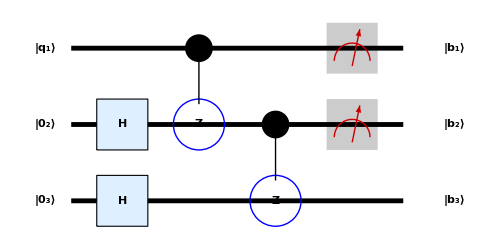

```mathematica
(* Draw circuit *)
nqset=1;
initialKets[matr_]:=initialKetsA[matr];
mat=({{1, C, 1, M}, {H, CZ, C, M}, {H, 1, CZ, 1}});
Circuit[mat,{}]
```

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1, s2 *)
mout={RandomInteger[],RandomInteger[]};

(* Initialize the density matrix for 3 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[3,1,2].CPHASE[3,2,3];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρ1]
```

Measurement outcomes = {0,0}

Identity gate: True

### 5-qubit chain

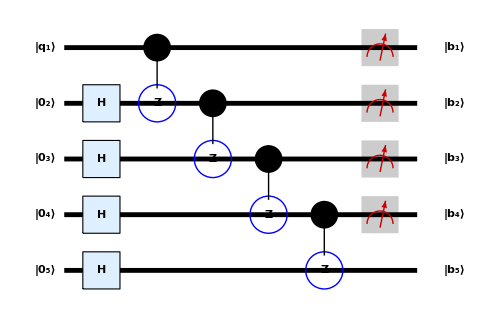

```mathematica
(* Draw circuit *)
nqset=1;
initialKets[matr_]:=initialKetsA[matr];
mat=({{1, C, 1, 1, 1, M}, {H, CZ, C, 1, 1, M}, {H, 1, CZ, C, 1, M}, {H, 1, 1, CZ, C, M}, {H, 1, 1, 1, CZ, 1}});
Circuit[mat,{}]
```

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1 - s4 *)
mout={RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[]};

(* Initialize the density matrix for 5 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,2].CPHASE[5,2,3].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2, 3, 4 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗PX[mout[[3]]]⊗PX[mout[[4]]]⊗𝕀] ;
ρM=Chop[PTr[{1,2,3,4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[4]]].MatrixPower[s[3],mout[[3]]].MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρ1]
```

Measurement outcomes = {0,0,1,1}

Identity gate: True

### 5-qubit chain (in the refreshing scheme)

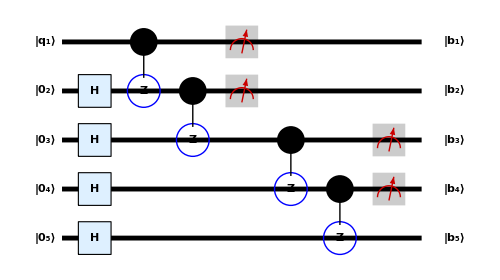

```mathematica
(* Draw circuit *)
nqset=1;
initialKets[matr_]:=initialKetsA[matr];
mat=({{1, C, 1, M, 1, 1, 1}, {H, CZ, C, M, 1, 1, 1}, {H, 1, CZ, 1, C, 1, M}, {H, 1, 1, 1, CZ, C, M}, {H, 1, 1, 1, 1, CZ, 1}});
Circuit[mat,{}]
```

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1 - s4 *)
mout={RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[]};

(* Step 1: {{1, 2, 3, □, □}} -> {{X, X, 3, □, □}} *)

(* Initialize the density matrix for 3 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[3,1,2].CPHASE[3,2,3];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀] ;
ρM1=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 2: {{X, X, 3, 4, 5}} -> {{X, X, X, X, 5}} *)

(* Initialize the density matrix for 3 qubits *)
ρT=AF[ρM1⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[3,1,2].CPHASE[3,2,3];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[3]]]⊗PX[mout[[4]]]⊗𝕀] ;
ρM2=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[4]]].MatrixPower[s[3],mout[[3]]].MatrixPower[s[1],mout[[2]]].MatrixPower[s[3],mout[[1]]];
ρOut=Chop[Byproduct.ρM2.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Measurement outcomes = ", mout];
Print["Identity gate: ",ρOut==ρ1]
```

Measurement outcomes = {1,0,1,1}

Identity gate: True

## Rotation gate

```mathematica
φ=.;
G0={Cos[φ],Sin[φ],0};
FullSimplify[ProjG[0,G0]]
FullSimplify[ProjG[1,G0]]
```

(1/2 | ⅇ^(-ⅈ φ)/(2 √(Abs[Cos[φ]]^2+Abs[Sin[φ]]^2))
ⅇ^(ⅈ φ)/(2 √(Abs[Cos[φ]]^2+Abs[Sin[φ]]^2)) | 1/2)

(1/2 | -ⅇ^(-ⅈ φ)/(2 √(Abs[Cos[φ]]^2+Abs[Sin[φ]]^2))
-ⅇ^(ⅈ φ)/(2 √(Abs[Cos[φ]]^2+Abs[Sin[φ]]^2)) | 1/2)

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1 - s4 *)
mout={RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[]};

(* {{1, 2, 3, 4, 5}} -> {{X, α', β', γ', □}} *)

(* Initialize the density matrix for 5 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,2].CPHASE[5,2,3].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2, 3, 4 in X basis *)
α=Pi/2;
β=-Pi/2;
γ=-Pi/2;
α0=-(-1)^mout[[1]]α;
β0=-(-1)^mout[[2]]β;
γ0=-(-1)^(mout[[1]]+mout[[3]])γ;
G2={Cos[α0],Sin[α0],0};
G3={Cos[β0],Sin[β0],0};
G4={Cos[γ0],Sin[γ0],0};
Proj=AF[PX[mout[[1]]]⊗ProjG[mout[[2]],G2]⊗ProjG[mout[[3]],G3]⊗ProjG[mout[[4]],G4]⊗𝕀] ;
ρM=Chop[PTr[{1,2,3,4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=MatrixPower[s[1],mout[[2]]+mout[[4]]].MatrixPower[s[3],mout[[1]]+mout[[3]]];
ρOut=Chop[Byproduct.ρM.Adj[Byproduct]];

(* Confirm the identity gate for measurement outcomes *)
Print["Output(on CBQC) = ",Chop[RotX[γ].RotZ[β].RotX[α].ρ1.ConjugateTranspose[RotX[γ].RotZ[β].RotX[α]]]];
Print["Output(on MBQC) = ",ρOut];
Print["for measurement outcomes = ", mout]
```

Output(on CBQC) = {{0.910381,0.236416-0.160298 ⅈ},{0.236416+0.160298 ⅈ,0.0896195}}

Output(on MBQC) = {{0.910381,0.236416-0.160298 ⅈ},{0.236416+0.160298 ⅈ,0.0896195}}

for measurement outcomes = {1,0,0,0}

## Two-qubit gates

### Swap gate

```mathematica
Swap=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}});
AF[s[0]⊗s[1]].Swap==Swap.AF[s[1]⊗s[0]]
AF[s[0]⊗s[2]].Swap==Swap.AF[s[2]⊗s[0]]
AF[s[0]⊗s[3]].Swap==Swap.AF[s[3]⊗s[0]]
AF[s[1]⊗s[2]].Swap==Swap.AF[s[2]⊗s[1]]
AF[s[1]⊗s[3]].Swap==Swap.AF[s[3]⊗s[1]]
AF[s[2]⊗s[3]].Swap==Swap.AF[s[3]⊗s[2]]
```

True

True

True

«3 more identical outputs»

```mathematica
(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1 - s10 *)
mout={RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],
RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[]};

(* Step 1: {{1, 3, □, □, □}, {□, 4, □, □, □}, {2, 5, □, □, □}} -> {{X, 3, □, □, □}, {□, 4, □, □, □}, {X, 5, □, □, □}} *)

(* Initialize the density matrix for 5 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρ2=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ2⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,3].CPHASE[5,2,5].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀⊗𝕀⊗𝕀] ;
ρM1=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 2: {{X, 3, 6, □, □}, {□, 4, 7, □, □}, {X, 5, 8, □, □}} -> {{X, X, 6, □, □}, {□, X, 7, □, □}, {X, X, 8, □, □}} *)

(* Initialize the density matrix for 6 qubits *)
ρT=AF[ρM1⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[6,1,4].CPHASE[6,2,5].CPHASE[6,3,6].CPHASE[6,4,5].CPHASE[6,5,6];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 3, 4, 5 in X basis *)
Proj=AF[PX[mout[[3]]]⊗PX[mout[[4]]]⊗PX[mout[[5]]]⊗𝕀⊗𝕀⊗𝕀] ;
ρM2=Chop[PTr[{1,2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 3: {{X, X, 6, 9, □}, {□, X, 7, □, □}, {X, X, 8, 10, □}} -> {{X, X, X, 9, □}, {□, X, X, □, □}, {X, X, X, 10, □}} *)

(* Initialize the density matrix for 5 qubits *)
ρT=AF[ρM2⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,4].CPHASE[5,3,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 6, 7, 8 in X basis *)
Proj=AF[PX[mout[[6]]]⊗PX[mout[[7]]]⊗PX[mout[[8]]]⊗𝕀⊗𝕀] ;
ρM3=Chop[PTr[{1,2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 4: {{X, X, X, 9, 11}, {□, X, X, □, □}, {X, X, X, 10, 12}} -> {{X, X, X, X, 11}, {□, X, X, □, □}, {X, X, X, X, 12}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM3⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[4,1,3].CPHASE[4,2,4];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 9, 10 in X basis *)
Proj=AF[PX[mout[[9]]]⊗PX[mout[[10]]]⊗𝕀⊗𝕀] ;
ρM4=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=AF[(MatrixPower[s[3],mout[[2]]+mout[[4]]+mout[[6]]].MatrixPower[s[1],mout[[5]]+mout[[7]]+mout[[9]]])⊗(MatrixPower[s[3],mout[[1]]+mout[[4]]+mout[[8]]].MatrixPower[s[1],mout[[3]]+mout[[7]]+mout[[10]]])];
ρOut=Chop[Byproduct.ρM4.Adj[Byproduct]];

(* Confirm the swap gate for measurement outcomes *)
Print["Output(on CBQC) = ",Chop[Swap.AF[ρ1⊗ρ2].ConjugateTranspose[Swap]]];
Print["Output(on MBQC) = ",ρOut];
Print["for measurement outcomes = ", mout]
```

Output(on CBQC) = {{0.064557,0.00574902-0.0931329 ⅈ,0.0613977+0.113845 ⅈ,0.169705-0.078437 ⅈ},{0.00574902+0.0931329 ⅈ,0.13487,-0.15877+0.0987135 ⅈ,0.12827+0.23784 ⅈ},{0.0613977-0.113845 ⅈ,-0.15877-0.0987135 ⅈ,0.259155,0.0230787-0.37387 ⅈ},{0.169705+0.078437 ⅈ,0.12827-0.23784 ⅈ,0.0230787+0.37387 ⅈ,0.541418}}

Output(on MBQC) = {{0.064557,0.00574902-0.0931329 ⅈ,0.0613977+0.113845 ⅈ,0.169705-0.078437 ⅈ},{0.00574902+0.0931329 ⅈ,0.13487,-0.15877+0.0987135 ⅈ,0.12827+0.23784 ⅈ},{0.0613977-0.113845 ⅈ,-0.15877-0.0987135 ⅈ,0.259155,0.0230787-0.37387 ⅈ},{0.169705+0.078437 ⅈ,0.12827-0.23784 ⅈ,0.0230787+0.37387 ⅈ,0.541418}}

for measurement outcomes = {1,0,0,1,1,1,1,1,0,1}

### Ising coupling gate

```mathematica
(* Set up time variable *)
ϕ=0.1;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes s1 - s20 *)
mout={RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],
RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[],RandomInteger[]};

(* Step 1: {{1, 3, □, □, □, □, □, □, □}, {□, 4, □, □, □, □, □, □, □}, {2, 5, □, □, □, □, □, □, □}} -> {{X, 3, □, □, □, □, □, □, □}, {□, 4, □, □, □, □, □, □, □}, {X, 5, □, □, □, □, □, □, □}} *)

(* Initialize the density matrix for 5 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρ2=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ2⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,3].CPHASE[5,2,5].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1, 2 in X basis *)
Proj=AF[PX[mout[[1]]]⊗PX[mout[[2]]]⊗𝕀⊗𝕀⊗𝕀];
ρM1=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 2: {{X, 3, 6, □, □, □, □, □, □}, {□, 4, 7, □, □, □, □, □, □}, {X, 5, 8, □, □, □, □, □, □}} -> {{X, X, 6, □, □, □, □, □, □}, {□, X, 7, □, □, □, □, □, □}, {X, X, 8, □, □, □, □, □, □}} *)

(* Initialize the density matrix for 6 qubits *)
ρT=AF[ρM1⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[6,1,4].CPHASE[6,2,5].CPHASE[6,3,6].CPHASE[6,4,5].CPHASE[6,5,6];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 3, 4, 5 in X basis *)
Proj=AF[PX[mout[[3]]]⊗PX[mout[[4]]]⊗PX[mout[[5]]]⊗𝕀⊗𝕀⊗𝕀];
ρM2=Chop[PTr[{1,2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 3: {{X, X, 6, 9, □, □, □, □, □}, {□, X, 7, □, □, □, □, □, □}, {X, X, 8, 10, □, □, □, □, □}} -> {{X, X, X, 9, □, □, □, □, □}, {□, X, X, □, □, □, □, □, □}, {X, X, X, 10, □, □, □, □, □}} *)

(* Initialize the density matrix for 5 qubits *)
ρT=AF[ρM2⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,4].CPHASE[5,3,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 6, 7, 8 in X basis *)
Proj=AF[PX[mout[[6]]]⊗PX[mout[[7]]]⊗PX[mout[[8]]]⊗𝕀⊗𝕀];
ρM3=Chop[PTr[{1,2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 4: {{X, X, X, 9, 11, □, □, □, □}, {□, X, X, □, □, □, □, □, □}, {X, X, X, 10, 12, □, □, □, □}} -> {{X, X, X, X, 11, □, □, □, □}, {□, X, X, □, □, □, □, □, □}, {X, X, X, X, 12, □, □, □, □}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM3⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[4,1,3].CPHASE[4,2,4];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 9, 10 in X basis *)
Proj=AF[PX[mout[[9]]]⊗PX[mout[[10]]]⊗𝕀⊗𝕀];
ρM4=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 5: {{X, X, X, X, 11, 13, □, □, □}, {□, X, X, □, □, 14, □, □, □}, {X, X, X, X, 12, 15, □, □, □}} -> {{X, X, X, X, X, 13, □, □, □}, {□, X, X, □, □, 14, □, □, □}, {X, X, X, X, X, 15, □, □, □}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM4⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,3].CPHASE[5,2,5].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 11, 12 in X basis *)
Proj=AF[PX[mout[[11]]]⊗PX[mout[[12]]]⊗𝕀⊗𝕀⊗𝕀];
ρM5=Chop[PTr[{1,2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 6: {{X, X, X, X, X, 13, 16, □, □}, {□, X, X, □, □, 14, 17, □, □}, {X, X, X, X, X, 15, 18, □, □}} -> {{X, X, X, X, X, X, 16, □, □}, {□, X, X, □, □, 14, X, □, □}, {X, X, X, X, X, X, 18, □, □}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM5⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[6,1,4].CPHASE[6,2,5].CPHASE[6,3,6].CPHASE[6,4,5].CPHASE[6,5,6];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 13, 15, 17 in X basis *)
Proj=AF[PX[mout[[13]]]⊗𝕀⊗PX[mout[[15]]]⊗𝕀⊗PX[mout[[17]]]⊗𝕀];
ρM6=Chop[PTr[{1,3,5},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 7: {{X, X, X, X, X, X, 16, 19, □}, {□, X, X, □, □, 14, X, □, □}, {X, X, X, X, X, X, 18, 20, □}} -> {{X, X, X, X, X, X, X, 19, □}, {□, X, X, □, □, 14, X, □, □}, {X, X, X, X, X, X, X, 20, □}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM6⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,2,4].CPHASE[5,3,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 16, 18 in X basis *)
Proj=AF[𝕀⊗PX[mout[[16]]]⊗PX[mout[[18]]]⊗𝕀⊗𝕀];
ρM7=Chop[PTr[{2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 8: {{X, X, X, X, X, X, X, 19, 21}, {□, X, X, □, □, 14, X, □, □}, {X, X, X, X, X, X, X, 20, 22}} -> {{X, X, X, X, X, X, X, X, 21}, {□, X, X, □, □, ϕ', X, □, □}, {X, X, X, X, X, X, X, X, 22}} *)

(* Initialize the density matrix for 4 qubits *)
ρT=AF[ρM7⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,2,4].CPHASE[5,3,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 16, 18 in X basis and qubit 14 in B(ϕ') basis *)
ϕ0=(-1)^(mout[[3]]+mout[[5]]+mout[[9]]+mout[[10]]+mout[[13]]+mout[[15]]+mout[[17]])2ϕ;
G14={Cos[ϕ0],Sin[ϕ0],0};
Proj=AF[ProjG[mout[[14]],G14]⊗PX[mout[[19]]]⊗PX[mout[[20]]]⊗𝕀⊗𝕀];
ρM8=Chop[PTr[{1,2,3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=AF[(MatrixPower[s[3],mout[[1]]+mout[[4]]+mout[[8]]+mout[[12]]+mout[[14]]+mout[[16]]].MatrixPower[s[1],mout[[3]]+mout[[7]]+mout[[10]]+mout[[15]]+mout[[17]]+mout[[19]]])⊗(MatrixPower[s[3],mout[[2]]+mout[[4]]+mout[[6]]+mout[[11]]+mout[[14]]+mout[[18]]].MatrixPower[s[1],mout[[5]]+mout[[7]]+mout[[9]]+mout[[13]]+mout[[17]]+mout[[20]]])];
ρOut=Chop[Byproduct.ρM8.Adj[Byproduct]];

(* Confirm the Ising coupling gate for measurement outcomes *)
Ising=MatrixExp[I ϕ AF[s[3]⊗s[3]]];
Print[Chop[Ising.AF[ρ1⊗ρ2].ConjugateTranspose[Ising]]];
Print[ρOut];
Print["for measurement outcomes = ", mout]
```

{{0.465614,0.225422-0.11255 ⅈ,0.29852+0.232901 ⅈ,0.200779-0.0408116 ⅈ},{0.225422+0.11255 ⅈ,0.136342,0.0882269+0.184916 ⅈ,0.10707+0.0287748 ⅈ},{0.29852-0.232901 ⅈ,0.0882269-0.184916 ⅈ,0.307888,0.108312-0.126596 ⅈ},{0.200779+0.0408116 ⅈ,0.10707-0.0287748 ⅈ,0.108312+0.126596 ⅈ,0.090156}}

{{0.465614,0.225422-0.11255 ⅈ,0.29852+0.232901 ⅈ,0.200779-0.0408116 ⅈ},{0.225422+0.11255 ⅈ,0.136342,0.0882269+0.184916 ⅈ,0.10707+0.0287748 ⅈ},{0.29852-0.232901 ⅈ,0.0882269-0.184916 ⅈ,0.307888,0.108312-0.126596 ⅈ},{0.200779+0.0408116 ⅈ,0.10707-0.0287748 ⅈ,0.108312+0.126596 ⅈ,0.090156}}

for measurement outcomes = {1,0,1,0,0,1,0,0,0,1,0,0,1,0,0,0,1,0,0,1}

## 1D Kitaev model

### State vector vs. density matrix

```mathematica
A=.;
B=.;
Ac=.;
Bc=.;
({{A}, {B}}).({{Ac, Bc}})
```

(Cos[ϕ] | 0 | 0 | ⅈ Sin[ϕ]
0 | Cos[ϕ] | ⅈ Sin[ϕ] | 0
0 | ⅈ Sin[ϕ] | Cos[ϕ] | 0
ⅈ Sin[ϕ] | 0 | 0 | Cos[ϕ])

(ⅇ^(ⅈ ϕ) | 0 | 0 | 0
0 | ⅇ^(-ⅈ ϕ) | 0 | 0
0 | 0 | ⅇ^(-ⅈ ϕ) | 0
0 | 0 | 0 | ⅇ^(ⅈ ϕ))

(1/2 | 1/2 | 1/2 | 1/2
-1/2 | 1/2 | -1/2 | 1/2
-1/2 | -1/2 | 1/2 | 1/2
1/2 | -1/2 | -1/2 | 1/2)

```mathematica
ϕ=.;
FullSimplify[AF[ConjugateTranspose[MatrixExp[I Pi/4 s[2]]]⊗ConjugateTranspose[MatrixExp[I Pi/4 s[2]]]].MatrixExp[I ϕ AF[s[3]⊗s[3]]].AF[MatrixExp[I Pi/4 s[2]]⊗MatrixExp[I Pi/4 s[2]]]]
```

(Cos[ϕ] | 0 | 0 | ⅈ Sin[ϕ]
0 | Cos[ϕ] | ⅈ Sin[ϕ] | 0
0 | ⅈ Sin[ϕ] | Cos[ϕ] | 0
ⅈ Sin[ϕ] | 0 | 0 | Cos[ϕ])

```mathematica
MatrixExp[I Pi/4 s[2]]
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

```mathematica
FullSimplify[MatrixExp[-I Pi/4 s[1]].MatrixExp[-I Pi/4 s[3]].MatrixExp[I Pi/4 s[1]]]
```

(1/(√2) | 1/(√2)
-1/(√2) | 1/(√2))

```mathematica
ConjugateTranspose[MatrixExp[I Pi/4 s[2]]]
MatrixExp[-I Pi/4 s[2]]
FullSimplify[ConjugateTranspose[MatrixExp[-I Pi/4 s[1]].MatrixExp[-I Pi/4 s[3]].MatrixExp[I Pi/4 s[1]]]]
FullSimplify[MatrixExp[-I Pi/4 s[1]].MatrixExp[I Pi/4 s[3]].MatrixExp[I Pi/4 s[1]]]
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

«1 more identical outputs»

```mathematica
MatrixExp[-I Pi/4 s[2]]
FullSimplify[ConjugateTranspose[MatrixExp[-I Pi/4 s[1]]].MatrixExp[-I Pi/4 s[3]].MatrixExp[-I Pi/4 s[1]]]
```

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

(1/(√2) | -1/(√2)
1/(√2) | 1/(√2))

```mathematica
ϵ=.;
FullSimplify[RotX[Pi/2].RotZ[ϵ].RotX[-Pi/2]]
RotY[-ϵ]
```

(Cos[ϵ/2] | Sin[ϵ/2]
-Sin[ϵ/2] | Cos[ϵ/2])

(Cos[ϵ/2] | Sin[ϵ/2]
-Sin[ϵ/2] | Cos[ϵ/2])

```mathematica
ϵ=.;
FullSimplify[RotZ[-Pi/2].RotX[ϵ].RotZ[Pi/2]]
RotY[-ϵ]
```

(Cos[ϵ/2] | Sin[ϵ/2]
-Sin[ϵ/2] | Cos[ϵ/2])

(Cos[ϵ/2] | Sin[ϵ/2]
-Sin[ϵ/2] | Cos[ϵ/2])

```mathematica
ϵ=.;
FullSimplify[RotX[Pi/2].RotY[-ϵ].RotX[-Pi/2]]
RotZ[-ϵ]
```

(ⅇ^((ⅈ ϵ)/2) | 0
0 | ⅇ^(-(ⅈ ϵ)/2))

(ⅇ^((ⅈ ϵ)/2) | 0
0 | ⅇ^(-(ⅈ ϵ)/2))

### Test

```mathematica
(* Set up control parameters *)
ϕ=0.1;
g=0.2;
Nc=4;

ρ1=AF[Chop[ρ[RandomKet1]]];
ρ2=AF[Chop[ρ[RandomKet1]]];
ρ3=AF[Chop[ρ[RandomKet1]]];
ρ4=AF[Chop[ρ[RandomKet1]]];

(* Build up the output ket vector for the circuit model *)
GateN=AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(Nc-2)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(1)]].AF[IdentityMatrix[2^(Nc-2)]⊗MatrixExp[I ϕ AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
If[Nc≥3,
For[j=Nc-2,j≥2,j--,
GateN=GateN.AF[IdentityMatrix[2^(j-1)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-j)]].AF[IdentityMatrix[2^(j-1)]⊗MatrixExp[I ϕ AF[s[3]⊗s[3]]]⊗IdentityMatrix[2^(Nc-j-1)]].AF[IdentityMatrix[2^(j)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-j-1)]]
];
GateN=GateN.AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-1)]].AF[MatrixExp[I ϕ AF[s[3]⊗s[3]]]⊗IdentityMatrix[2^(Nc-2)]].AF[IdentityMatrix[2^(1)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-2)]]
];
GateN=GateN.AF[(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-1)]];

ρOutCir=Chop[GateN.AF[ρ1⊗ρ2⊗ρ3⊗ρ4].Adj[GateN]];
KetOutCir=Table[ρOutCir[[j,1]]/(√ρOutCir[[1,1]]),{j,1,2^Nc}];

(* Print the result *)
Print["CBQC: ", KetOutCir]
```

CBQC: {0.286311,0.0736988-0.302508 ⅈ,-0.0114957+0.250389 ⅈ,0.218217+0.165409 ⅈ,0.394485+0.110014 ⅈ,0.220027-0.378167 ⅈ,-0.0684043+0.308829 ⅈ,0.223912+0.255917 ⅈ,-0.0783291-0.0556407 ⅈ,-0.080002+0.0688581 ⅈ,0.0559344-0.0622151 ⅈ,-0.021885-0.0900443 ⅈ,-0.0582978-0.134858 ⅈ,-0.154493+0.0234485 ⅈ,0.0980358-0.0525361 ⅈ,0.0175084-0.117518 ⅈ}

### Generalization to the large-N gate

```mathematica
(* Set up control parameters *)
ϕ=0.1;
g=0.2;
Nc=3;

(* Prepare qubit in X+ basis *)
ρ0=AF[ρ[KetX[0]]];

(* Random generation of measurement outcomes
{{1, 2, 3, 4, □}}
{{□, □, □, □, 5, 6, 7, 8, □, □, □, □, □}, {□, □, □, □, □, 9, 10, □, □, □, □, □, □}, {11, 12, 13, 14, 15, 16, 17, 18, 19, 20, 21, 22, □}} 
with each index increased by 18(j-1) for the jth run
{{23, 24, 25, 26, □}} 
with each index increased by 18(Nc-2) *)
mout=RandomInteger[1,8+18(Nc-1)];

(* Step 1: 
{{1((1)), 2((2)), 3((3)), 4((4)), ((5)), □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}} 
-> {{X, Subscript[α, 1]', Subscript[β, 1]', Subscript[ϕ, 1]', ((5)), □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}} *)

(* Initialize the density matrix for 5 qubits *)
ρ1=AF[Chop[ρ[RandomKet1]]];
ρT=AF[ρ1⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Define the total initial density matrix *)
ρIn=ρ1;

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,2].CPHASE[5,2,3].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 1 in X basis, 2 in B(Subscript[α, 2]'), 3 in B(Subscript[β, 2]'), and 4 in B(Subscript[ϕ, 2]') basis *)
α0=(-1)^mout[[1]] Pi/2;
β0=-(-1)^mout[[2]]Pi/2;
ϕ0=-(-1)^(mout[[1]]+mout[[3]])(2g ϕ+Pi/2);
G2={Cos[α0],Sin[α0],0};
G3={Cos[β0],Sin[β0],0};
G4={Cos[ϕ0],Sin[ϕ0],0};
Proj=AF[PX[mout[[1]]]⊗ProjG[mout[[2]],G2]⊗ProjG[mout[[3]],G3]⊗ProjG[mout[[4]],G4]⊗𝕀] ;
ρOut=Chop[PTr[{1,2,3,4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Loop for the recurrent part *)
For[j=1,j≤Nc-1,j++,

(* Step 2: 
{{□, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}, {11+18(j-1)
((1)), 12+18(j-1)
((2)), 13+18(j-1)
((3)), 14+18(j-1)
((4)), ((5)), □, □, □, □, □, □, □, □}} 
-> {{□, □, □, □, □, □, □, □, □, □, □, □, □}, {□, □, □, □, □, □, □, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', ((5)), □, □, □, □, □, □, □, □}} *)

(* Define the total initial density matrix *)
ρj=AF[Chop[ρ[RandomKet1]]];
ρIn=AF[ρIn⊗ρj];

(* Initialize the density matrix for 5 qubits *)
ρT=AF[ρj⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[5,1,2].CPHASE[5,2,3].CPHASE[5,3,4].CPHASE[5,4,5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 11 in X basis, 12 in B(Subscript[α, j+1]'), 13 in B(Subscript[β, j+1]'), and 14 in B(Subscript[ϕ, j+1]') basis *)
α0=(-1)^mout[[11+18(j-1)]] Pi/2;
β0=-(-1)^mout[[12+18(j-1)]]Pi/2;
ϕ0=-(-1)^(mout[[11+18(j-1)]]+mout[[13+18(j-1)]])(2g ϕ+Pi/2);
G12={Cos[α0],Sin[α0],0};
G13={Cos[β0],Sin[β0],0};
G14={Cos[ϕ0],Sin[ϕ0],0};
Proj=AF[PX[mout[[11+18(j-1)]]]⊗ProjG[mout[[12+18(j-1)]],G12]⊗ProjG[mout[[13+18(j-1)]],G13]⊗ProjG[mout[[14+18(j-1)]],G14]⊗𝕀];
ρM2=Chop[PTr[{1,2,3,4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 3: 
Extra qubits(1,...,j-1)(j≥2)+
{{□, □, □, □, 5+18(j-1)
((j)), ((j+2)), □, □, □, □, □, □, □}, {□, □, □, □, □, ((j+3)), □, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', 15+18(j-1)
((j+1)), ((j+4)), □, □, □, □, □, □, □}} 
-> {{□, □, □, □, X, ((j+2)), □, □, □, □, □, □, □}, {□, □, □, □, □, ((j+3)), □, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, ((j+4)), □, □, □, □, □, □, □}} *)

(* Initialize the density matrix for 5(+extra) qubits *)
ρT=AF[ρOut⊗ρM2⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[j+4,j,j+2].CPHASE[j+4,j+1,j+4].CPHASE[j+4,j+2,j+3].CPHASE[j+4,j+3,j+4];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 5, 15 in X basis *)
Proj=If[j==1,
AF[PX[mout[[5]]]⊗PX[mout[[15]]]⊗𝕀⊗𝕀⊗𝕀],
AF[IdentityMatrix[2^(j-1)]⊗PX[mout[[5+18(j-1)]]]⊗PX[mout[[15+18(j-1)]]]⊗𝕀⊗𝕀⊗𝕀]];
ρM3=Chop[PTr[{j,j+1},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 4: 
Extra qubits(1,...,j-1)(j≥2)+
{{□, □, □, □, X, 6+18(j-1)
((j)), ((j+3)), □, □, □, □, □, □}, {□, □, □, □, □, ((j+1)), 10+18(j-1)
((j+4)), □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, 16+18(j-1)
((j+2)), ((j+5)), □, □, □, □, □, □}} 
-> {{□, □, □, □, X, X, ((j+3)), □, □, □, □, □, □}, {□, □, □, □, □, ((j+1)), X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, ((j+5)), □, □, □, □, □, □}} *)

(* Initialize the density matrix for 6(+extra) qubits *)
ρT=AF[ρM3⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[j+5,j,j+3].CPHASE[j+5,j+1,j+4].CPHASE[j+5,j+2,j+5].CPHASE[j+5,j+3,j+4].CPHASE[j+5,j+4,j+5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 6, 10, 16 in X basis *)
Proj=If[j==1,
AF[PX[mout[[6]]]⊗𝕀⊗PX[mout[[16]]]⊗𝕀⊗PX[mout[[10]]]⊗𝕀],
AF[IdentityMatrix[2^(j-1)]⊗PX[mout[[6+18(j-1)]]]⊗𝕀⊗PX[mout[[16+18(j-1)]]]⊗𝕀⊗PX[mout[[10+18(j-1)]]]⊗𝕀]];
ρM4=Chop[PTr[{j,j+2,j+4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 5: 
Extra qubits(1,...,j-1)(j≥2)+
{{□, □, □, □, X, X, 7+18(j-1)
((j+1)), 8+18(j-1)
((j+3)), ((j+4)), □, □, □, □}, {□, □, □, □, □, 9+18(j-1)
((j)), X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, ((j+2)), □, □, □, □, □, □}} 
-> {{□, □, □, □, X, X, X, X, ((j+4)), □, □, □, □}, {□, □, □, □, □, Subscript[ϕ, j,j+1]^", X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, ((j+2)), □, □, □, □, □, □}} *)

(* Initialize the density matrix for 5(+extra) qubits *)
ρT=AF[ρM4⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[j+4,j+1,j+3].CPHASE[j+4,j+3,j+4];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 9 in B(Subscript[ϕ, j,j+1]^") and 7, 8 in X basis *)
ϕ0=If[j==1,
(-1)^(mout[[2]]+mout[[4]])(-1)^(mout[[6]]+mout[[10]]+mout[[12]]+mout[[14]]+mout[[16]])2ϕ,
(-1)^(mout[[12+18(j-2)]]+mout[[14+18(j-2)]]+mout[[16+18(j-2)]]+mout[[10+18(j-2)]]+mout[[8+18(j-2)]])(-1)^(mout[[6+18(j-1)]]+mout[[10+18(j-1)]]+mout[[12+18(j-1)]]+mout[[14+18(j-1)]]+mout[[16+18(j-1)]])2ϕ];
G9={Cos[ϕ0],Sin[ϕ0],0};
Proj=If[j==1,
AF[ProjG[mout[[9]],G9]⊗PX[mout[[7]]]⊗𝕀⊗PX[mout[[8]]]⊗𝕀],
AF[IdentityMatrix[2^(j-1)]⊗ProjG[mout[[9+18(j-1)]],G9]⊗PX[mout[[7+18(j-1)]]]⊗𝕀⊗PX[mout[[8+18(j-1)]]]⊗𝕀]];
ρM5=Chop[PTr[{j,j+1,j+3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 6: 
Extra qubits(1,...,j-1)(j≥2)+
{{□, □, □, □, X, X, X, X, ((j+1)), □, □, □, □}, {□, □, □, □, □, Subscript[ϕ, j,j+1]^", X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, 17+18(j-1)
((j)), 18+18(j-1)
((j+2)), ((j+3)), □, □, □, □}}
-> {{□, □, □, □, X, X, X, X, ((j+1)), □, □, □, □}, {□, □, □, □, □, Subscript[ϕ, j,j+1]^", X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, X, X, ((j+3)), □, □, □, □}} *)

(* Initialize the density matrix for 4(+extra) qubits *)
ρT=AF[ρM5⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[j+3,j,j+2].CPHASE[j+3,j+2,j+3];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 17, 18 in X basis *)
Proj=If[j==1,
AF[PX[mout[[17]]]⊗𝕀⊗PX[mout[[18]]]⊗𝕀],
AF[IdentityMatrix[2^(j-1)]⊗PX[mout[[17+18(j-1)]]]⊗𝕀⊗PX[mout[[18+18(j-1)]]]⊗𝕀]];
ρM6=Chop[PTr[{j,j+2},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Step 7: 
Extra qubits(1,...,j-1)(j≥2)+
{{□, □, □, □, X, X, X, X, ((j)), □, □, □, □}, {□, □, □, □, □, Subscript[ϕ, j,j+1]^", X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, X, X, 19+18(j-1)
((j+1)), 20+18(j-1)
((j+2)), 21+18(j-1)
((j+3)), 22+18(j-1)
((j+4)), ((j+5))}}
-> {{□, □, □, □, X, X, X, X, ((j)), □, □, □, □}, {□, □, □, □, □, Subscript[ϕ, j,j+1]^", X, □, □, □, □, □, □}, {X, Subscript[α, j+1]', Subscript[β, j+1]', Subscript[ϕ, j+1]', X, X, X, X, X, Subscript[α, j]^", Subscript[β, j]^", Subscript[γ, j]^", ((j+5))}} *)

(* Initialize the density matrix for 6(+extra) qubits *)
ρT=AF[ρM6⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[j+5,j+1,j+2].CPHASE[j+5,j+2,j+3].CPHASE[j+5,j+3,j+4].CPHASE[j+5,j+4,j+5];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 19 in X basis, 20 in B(Subscript[α, j]^") basis, 21 in B(Subscript[β, j]^") basis, and 22 in B(Subscript[γ, j]^") basis *)
If[j==1,
α0=(-1)^(mout[[1]]+mout[[3]])(-1)^(mout[[5]]+mout[[9]]+mout[[17]]+mout[[19]])Pi/2;
β0=(-1)^(mout[[2]]+mout[[4]])(-1)^(mout[[6]]+mout[[10]]+mout[[18]]+mout[[20]])Pi/2;
γ0=-(-1)^(mout[[1]]+mout[[3]])(-1)^(mout[[5]]+mout[[9]]+mout[[17]]+mout[[19]]+mout[[21]])Pi/2,
α0=(-1)^(mout[[11+18(j-2)]]+mout[[13+18(j-2)]]+mout[[15+18(j-2)]]+mout[[9+18(j-2)]]+mout[[7+18(j-2)]])(-1)^(mout[[5+18(j-1)]]+mout[[9+18(j-1)]]+mout[[17+18(j-1)]]+mout[[19+18(j-1)]])Pi/2;
β0=(-1)^(mout[[12+18(j-2)]]+mout[[14+18(j-2)]]+mout[[16+18(j-2)]]+mout[[10+18(j-2)]]+mout[[8+18(j-2)]])(-1)^(mout[[6+18(j-1)]]+mout[[10+18(j-1)]]+mout[[18+18(j-1)]]+mout[[20+18(j-1)]])Pi/2;
γ0=-(-1)^(mout[[11+18(j-2)]]+mout[[13+18(j-2)]]+mout[[15+18(j-2)]]+mout[[9+18(j-2)]]+mout[[7+18(j-2)]])(-1)^(mout[[5+18(j-1)]]+mout[[9+18(j-1)]]+mout[[17+18(j-1)]]+mout[[19+18(j-1)]]+mout[[21+18(j-1)]])Pi/2];
G20={Cos[α0],Sin[α0],0};
G21={Cos[β0],Sin[β0],0};
G22={Cos[γ0],Sin[γ0],0};
Proj=If[j==1,
AF[𝕀⊗PX[mout[[19]]]⊗ProjG[mout[[20]],G20]⊗ProjG[mout[[21]],G21]⊗ProjG[mout[[22]],G22]⊗𝕀],
AF[IdentityMatrix[2^(j-1)]⊗𝕀⊗PX[mout[[19+18(j-1)]]]⊗ProjG[mout[[20+18(j-1)]],G20]⊗ProjG[mout[[21+18(j-1)]],G21]⊗ProjG[mout[[22+18(j-1)]],G22]⊗𝕀]];
ρOut=Chop[PTr[{j+1,j+2,j+3,j+4},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Apply Swap gate to rearrange the output ket vector in the same order as the input *)
If[j==1,
Swap=({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}}),
Swap=AF[IdentityMatrix[2^(j-1)]⊗({{1, 0, 0, 0}, {0, 0, 1, 0}, {0, 1, 0, 0}, {0, 0, 0, 1}})]];
ρOut=Chop[Swap.ρOut.Adj[Swap]]
];

(* Step 8: 
Extra qubits(1,...,Nc-1)+
{{23+18(Nc-2)
((Nc)), 24+18(Nc-2)
((Nc+1)), 25+18(Nc-2)
((Nc+2)), 26+18(Nc-2)
((Nc+3)), ((Nc+4))}}
-> {{X, Subscript[α, N]^", Subscript[β, N]^", Subscript[γ, N]^", ((Nc+4))}} *)

(* Initialize the density matrix for 5(+extra) qubits *)
ρT=AF[ρOut⊗ρ0⊗ρ0⊗ρ0⊗ρ0];

(* Entangle qubits via CZ gate *)
UCP=CPHASE[Nc+4,Nc,Nc+1].CPHASE[Nc+4,Nc+1,Nc+2].CPHASE[Nc+4,Nc+2,Nc+3].CPHASE[Nc+4,Nc+3,Nc+4];
ρCP=Chop[UCP.ρT.Adj[UCP]];

(* Measure qubit 23 in X basis, 24 in B(Subscript[α, N]^") basis, 25 in B(Subscript[β, N]^") basis, and 26 in B(Subscript[γ, N]^") basis *)
α0=(-1)^(mout[[11+18(Nc-2)]]+mout[[13+18(Nc-2)]]+mout[[15+18(Nc-2)]]+mout[[9+18(Nc-2)]]+mout[[7+18(Nc-2)]])(-1)^mout[[23+18(Nc-2)]] Pi/2;
β0=(-1)^(mout[[12+18(Nc-2)]]+mout[[14+18(Nc-2)]]+mout[[16+18(Nc-2)]]+mout[[10+18(Nc-2)]]+mout[[8+18(Nc-2)]])(-1)^mout[[24+18(Nc-2)]] Pi/2;
γ0=-(-1)^(mout[[11+18(Nc-2)]]+mout[[13+18(Nc-2)]]+mout[[15+18(Nc-2)]]+mout[[9+18(Nc-2)]]+mout[[7+18(Nc-2)]])(-1)^(mout[[23+18(Nc-2)]]+mout[[25+18(Nc-2)]])Pi/2;
G24={Cos[α0],Sin[α0],0};
G25={Cos[β0],Sin[β0],0};
G26={Cos[γ0],Sin[γ0],0};
Proj=AF[IdentityMatrix[2^(Nc-1)]⊗PX[mout[[23+18(Nc-2)]]]⊗ProjG[mout[[24+18(Nc-2)]],G24]⊗ProjG[mout[[25+18(Nc-2)]],G25]⊗ProjG[mout[[26+18(Nc-2)]],G26]⊗𝕀];
ρOut=Chop[PTr[{Nc,Nc+1,Nc+2,Nc+3},Proj.ρCP.Proj]/Tr[Proj.ρCP.Proj]];

(* Remove the byproduct operator from the result *)
Byproduct=Chop[MatrixPower[s[3],mout[[1]]+mout[[3]]+mout[[5]]+mout[[9]]+mout[[17]]+mout[[19]]+mout[[21]]].MatrixPower[s[1],mout[[2]]+mout[[4]]+mout[[6]]+mout[[10]]+mout[[18]]+mout[[20]]+mout[[22]]]];
If[Nc≥3,
For[j=2,j≤Nc-1,j++,
Byproduct=Chop[AF[Byproduct⊗(MatrixPower[s[3],mout[[11+18(j-2)]]+mout[[13+18(j-2)]]+mout[[15+18(j-2)]]+mout[[9+18(j-2)]]+mout[[7+18(j-2)]]+mout[[5+18(j-1)]]+mout[[9+18(j-1)]]+mout[[17+18(j-1)]]+mout[[19+18(j-1)]]+mout[[21+18(j-1)]]].MatrixPower[s[1],mout[[12+18(j-2)]]+mout[[14+18(j-2)]]+mout[[16+18(j-2)]]+mout[[10+18(j-2)]]+mout[[8+18(j-2)]]+mout[[6+18(j-1)]]+mout[[10+18(j-1)]]+mout[[18+18(j-1)]]+mout[[20+18(j-1)]]+mout[[22+18(j-1)]]])]]
]];
Byproduct=Chop[AF[Byproduct⊗(MatrixPower[s[3],mout[[11+18(Nc-2)]]+mout[[13+18(Nc-2)]]+mout[[15+18(Nc-2)]]+mout[[9+18(Nc-2)]]+mout[[7+18(Nc-2)]]+mout[[23+18(Nc-2)]]+mout[[25+18(Nc-2)]]].MatrixPower[s[1],mout[[12+18(Nc-2)]]+mout[[14+18(Nc-2)]]+mout[[16+18(Nc-2)]]+mout[[10+18(Nc-2)]]+mout[[8+18(Nc-2)]]+mout[[24+18(Nc-2)]]+mout[[26+18(Nc-2)]]])]];
ρOut=Chop[Byproduct.ρOut.Adj[Byproduct]];

(* Bulid up the output ket vector *)
KetOut=Table[ρOut[[j,1]]/(√ρOut[[1,1]]),{j,1,2^Nc}];

(* Build up the output ket vector for the circuit model *)
GateN=AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(Nc-2)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(1)]].AF[IdentityMatrix[2^(Nc-2)]⊗MatrixExp[I ϕ AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
If[Nc≥3,
For[j=Nc-2,j≥2,j--,
GateN=GateN.AF[IdentityMatrix[2^(j-1)]⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-j)]].AF[IdentityMatrix[2^(j-1)]⊗MatrixExp[I ϕ AF[s[3]⊗s[3]]]⊗IdentityMatrix[2^(Nc-j-1)]].AF[IdentityMatrix[2^(j)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-j-1)]]
];
GateN=GateN.AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-1)]].AF[MatrixExp[I ϕ AF[s[3]⊗s[3]]]⊗IdentityMatrix[2^(Nc-2)]].AF[IdentityMatrix[2^(1)]⊗(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-2)]]
];
GateN=GateN.AF[(MatrixExp[-I(g ϕ +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗IdentityMatrix[2^(Nc-1)]];

ρOutCir=Chop[GateN.ρIn.Adj[GateN]];
KetOutCir=Table[ρOutCir[[j,1]]/(√ρOutCir[[1,1]]),{j,1,2^Nc}];

(* Print the result *)
Print["CBQC: ", KetOutCir];
Print["MBQC: ", KetOut];
Print["for N = ", Nc, " and measurement outcomes = ", mout]
```

CBQC: {0.31555,0.294543-0.176243 ⅈ,-0.294493+0.349383 ⅈ,-0.138625+0.455563 ⅈ,-0.135061+0.180595 ⅈ,-0.0172902+0.236865 ⅈ,-0.190487-0.284473 ⅈ,-0.29196-0.193268 ⅈ}

MBQC: {0.31555,0.294543-0.176243 ⅈ,-0.294493+0.349383 ⅈ,-0.138625+0.455563 ⅈ,-0.135061+0.180595 ⅈ,-0.0172902+0.236865 ⅈ,-0.190487-0.284473 ⅈ,-0.29196-0.193268 ⅈ}

for N = 3 and measurement outcomes = {1,0,0,0,1,1,0,0,1,0,0,1,1,0,1,1,0,1,1,0,0,0,1,1,0,1,0,1,0,0,1,1,1,1,1,1,0,1,0,0,0,0,0,0}

### Test for Lie-Trotter product formula

```mathematica
ϕ=0.1;
g=0.5;

ResultExact=Chop[MatrixExp[I ϕ AF[s[1]⊗s[1]]+I g ϕ(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])]];

ResultM1=Chop[MatrixExp[I ϕ AF[s[1]⊗s[1]]].MatrixExp[I g ϕ(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])]];

M10=MatrixExp[I(ϕ/10)AF[s[1]⊗s[1]]].MatrixExp[I g(ϕ/10)(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])];
ResultM10=M10;
Do[ResultM10=ResultM10.M10,{j,1,9}];
ResultM10=Chop[ResultM10];

M20=MatrixExp[I(ϕ/20)AF[s[1]⊗s[1]]].MatrixExp[I g(ϕ/20)(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])];
ResultM20=M20;
Do[ResultM20=ResultM20.M20,{j,1,9}];
ResultM20=Chop[ResultM20.ResultM20];

M30=MatrixExp[I(ϕ/30)AF[s[1]⊗s[1]]].MatrixExp[I g(ϕ/30)(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])];
ResultM30=M30;
Do[ResultM30=ResultM30.M30,{j,1,9}];
ResultM30=Chop[ResultM30.ResultM30.ResultM30];

M40=MatrixExp[I(ϕ/40)AF[s[1]⊗s[1]]].MatrixExp[I g(ϕ/40)(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])];
ResultM40=M40;
Do[ResultM40=ResultM40.M40,{j,1,9}];
ResultM40=Chop[ResultM40.ResultM40.ResultM40.ResultM40];

M50=MatrixExp[I(ϕ/50)AF[s[1]⊗s[1]]].MatrixExp[I g(ϕ/50)(AF[𝕀⊗s[3]]+AF[s[3]⊗𝕀])];
ResultM50=M50;
Do[ResultM50=ResultM50.M50,{j,1,9}];
ResultM50=Chop[ResultM50.ResultM50.ResultM50.ResultM50.ResultM50];

Print["M_c=1: ",ResultM1//MatrixForm]
Print["M_c=10: ",ResultM10//MatrixForm]
Print["M_c=20: ",ResultM20//MatrixForm]
Print["M_c=30: ",ResultM30//MatrixForm]
Print["M_c=40: ",ResultM40//MatrixForm]
Print["M_c=50: ",ResultM50//MatrixForm]
Print["Exact: ",ResultExact//MatrixForm]
```

M_c=1: (0.990033+0.0993347 ⅈ | 0 | 0 | 0.00996671+0.0993347 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.00996671+0.0993347 ⅈ | 0 | 0 | 0.990033-0.0993347 ⅈ)

M_c=10: (0.990017+0.0996637 ⅈ | 0 | 0 | 0.00099667+0.0996637 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.00099667+0.0996637 ⅈ | 0 | 0 | 0.990017-0.0996637 ⅈ)

M_c=20: (0.990017+0.0996662 ⅈ | 0 | 0 | 0.000498335+0.0996662 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.000498335+0.0996662 ⅈ | 0 | 0 | 0.990017-0.0996662 ⅈ)

M_c=30: (0.990017+0.0996666 ⅈ | 0 | 0 | 0.000332223+0.0996666 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.000332223+0.0996666 ⅈ | 0 | 0 | 0.990017-0.0996666 ⅈ)

M_c=40: (0.990017+0.0996668 ⅈ | 0 | 0 | 0.000249168+0.0996668 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.000249168+0.0996668 ⅈ | 0 | 0 | 0.990017-0.0996668 ⅈ)

M_c=50: (0.990017+0.0996669 ⅈ | 0 | 0 | 0.000199334+0.0996669 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
-0.000199334+0.0996669 ⅈ | 0 | 0 | 0.990017-0.0996669 ⅈ)

Exact: (0.990017+0.099667 ⅈ | 0 | 0 | 0.+0.099667 ⅈ
0 | 0.995004 | 0.+0.0998334 ⅈ | 0
0 | 0.+0.0998334 ⅈ | 0.995004 | 0
0.+0.099667 ⅈ | 0 | 0 | 0.990017-0.099667 ⅈ)

### Test for discrete Fourier transform

```mathematica
t=.;
w=.;
E0=.;
FourierTransform[Exp[-I E0 t]/(√(2Pi)),t,w]
```

DiracDelta[E0-w]

```mathematica
η=.;
w=.;
Integrate[-I Exp[(I w-η)t],{t,0,∞}]
```

ConditionalExpression[-ⅈ/(-ⅈ w+η),Im[w]+Re[η]>0]

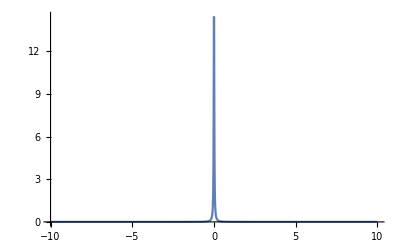

```mathematica
η=0.02;
Plot[-1/Pi Im[1/(w+I η)],{w,-10,10},AxesOrigin->{-10,0},PlotRange->Full]
```

```mathematica
dw=0.01;
E0=0;
η=0.02;
i0=2000;
Do[
GreenT=Table[t=(j-1)(2Pi)/(i*dw);-((2Pi)/(i*dw) √i)I Exp[-η t]Exp[-I E0 t],{j,1,i}];
If[i==i0,
GreenW=-1/Pi Fourier[GreenT];
GreenW0=GreenW[[1]],
GreenW=-1/Pi Fourier[GreenT];
If[Abs[Im[GreenW[[1]]-GreenW0]/Im[GreenW0]]<10^(-6),
Nt=i;Break[],
GreenW0=GreenW[[1]]]
],{i,i0,10^6}];
Print[Nt]
Print[Im[GreenW[[1]]]]
Print[1/Pi/0.02]
```

2507

15.9554

15.9155

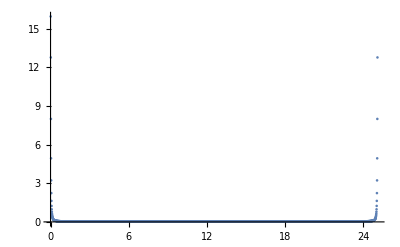

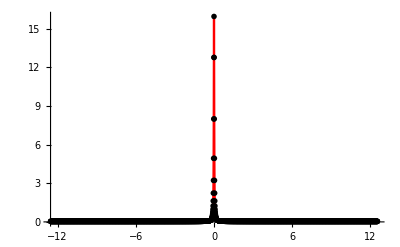

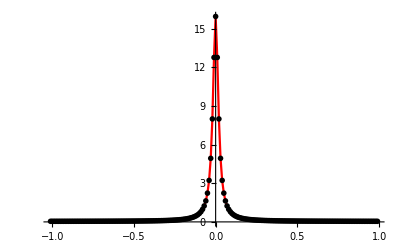

```mathematica
Nt=2508;(* to be even number *)
dw=0.01;
E0=0;
η=0.02;
GreenT=Table[t=(j-1)(2Pi)/(Nt*dw);-((2Pi)/(Nt*dw) √Nt)I Exp[-η t]Exp[-I E0 t],{j,1,Nt}];
GreenW=Fourier[GreenT];
ListPlot[Table[{j dw,-1/Pi Im[GreenW[[j]]]},{j,1,Nt}],Joined->False,PlotRange->All]
ListPlot[Table[{(j-(Nt/2+1))dw,If[j≤Nt/2,-1/Pi Im[GreenW[[j+Nt/2]]],-1/Pi Im[GreenW[[j-Nt/2]]]]},{j,1,Nt+1}],AxesOrigin->{-Nt/2 dw,0},Joined->True,PlotStyle->Red,Mesh->All,MeshStyle->{PointSize[0.01],Black},PlotRange->Full]
ListPlot[Table[{(j-(Nt/2+1))dw,If[j≤Nt/2,-1/Pi Im[GreenW[[j+Nt/2]]],-1/Pi Im[GreenW[[j-Nt/2]]]]},{j,Nt/2-100,Nt/2+100}],AxesOrigin->{0,0},Joined->True,PlotStyle->Red,Mesh->All,MeshStyle->{PointSize[0.01],Black},PlotRange->Full]
```

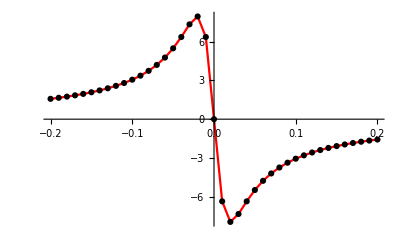

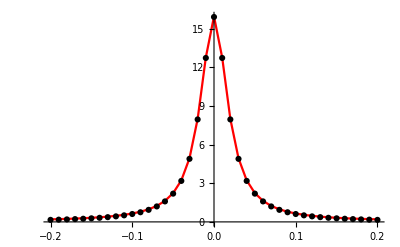

```mathematica
Nt=2508;(* to be even number *)
dw=0.01;
E0=0;
η=0.02;
R=20;
GreenT=Table[t=(j-1)(2Pi)/(Nt*dw);-((2Pi)/(Nt*dw) √Nt)I Exp[-η t]Exp[-I E0 t],{j,1,Nt}];
GreenW=Fourier[GreenT];
PR1=Table[{(j-(Nt/2+1))dw,If[j≤Nt/2,-1/Pi Re[GreenW[[j+Nt/2]]],-1/Pi Re[GreenW[[j-Nt/2]]]]},{j,(Nt/2+1)-R,(Nt/2+1)+R}];
PR2=Table[{(j-(Nt/2+1))dw,-1/Pi Re[1/((j-(Nt/2+1))dw+I η)]},{j,(Nt/2+1)-R,(Nt/2+1)+R}];
PI1=Table[{(j-(Nt/2+1))dw,If[j≤Nt/2,-1/Pi Im[GreenW[[j+Nt/2]]],-1/Pi Im[GreenW[[j-Nt/2]]]]},{j,(Nt/2+1)-R,(Nt/2+1)+R}];
PI2=Table[{(j-(Nt/2+1))dw,-1/Pi Im[1/((j-(Nt/2+1))dw+I η)]},{j,(Nt/2+1)-R,(Nt/2+1)+R}];
ListPlot[{PR1,PR2},AxesOrigin->Automatic,PlotRange->All,Joined->{True,False},PlotStyle->{Red,Black},PlotRange->Full]
ListPlot[{PI1,PI2},AxesOrigin->Automatic,PlotRange->All,Joined->{True,False},PlotStyle->{Red,Black},PlotRange->Full]
```

## Phase estimation for finding the spectral function; Exact

### Eigenvalues of ferromagnetic phase

```mathematica
Eigenvalues[AF[s[1]⊗s[1]]]
```

(-1
-1
1
1)

```mathematica
Eigenvalues[AF[s[1]⊗s[1]⊗𝕀+𝕀⊗s[1]⊗s[1]]]
```

(-2
-2
2
2
0
0
0
0)

```mathematica
Eigenvalues[AF[s[1]⊗s[1]⊗𝕀⊗𝕀+𝕀⊗s[1]⊗s[1]⊗𝕀+𝕀⊗𝕀⊗s[1]⊗s[1]]]
```

(-3
-3
3
3
-1
-1
-1
-1
-1
-1
1
1
1
1
1
1)

### Eigenvalues of paramagnetic phase

```mathematica
Eigenvalues[AF[s[3]⊗𝕀+𝕀⊗s[3]]]
```

(-2
2
0
0)

```mathematica
Eigenvalues[AF[s[3]⊗𝕀⊗𝕀+𝕀⊗s[3]⊗𝕀+𝕀⊗𝕀⊗s[3]]]
```

(-3
3
-1
-1
-1
1
1
1)

```mathematica
Eigenvalues[AF[s[3]⊗𝕀⊗𝕀⊗𝕀+𝕀⊗s[3]⊗𝕀⊗𝕀+𝕀⊗𝕀⊗s[3]⊗𝕀+𝕀⊗𝕀⊗𝕀⊗s[3]]]
```

(-4
4
-2
-2
-2
-2
2
2
2
2
0
0
0
0
0
0)

### Eigenvalues in general case

```mathematica
J=.;
g=.;
Eigenvalues[AF[-J s[1]⊗s[1]-J g s[3]⊗𝕀-J g 𝕀⊗s[3]]]
```

(-J
J
-√(1+4 g^2) J
√(1+4 g^2) J)

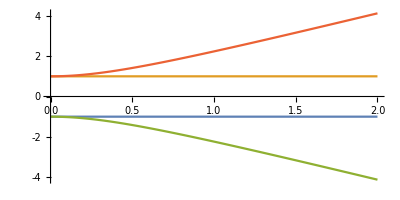

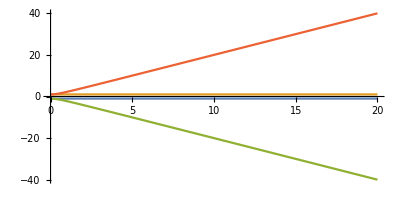

```mathematica
Plot[{-1,1,-√(1+4 g^2),√(1+4 g^2)},{g,0,2},AspectRatio->0.5,Ticks->{Automatic,{-4,-3,-2,-1,0,1,2,3,4}}]
Plot[{-1,1,-√(1+4 g^2),√(1+4 g^2)},{g,0,20},AspectRatio->0.5]
```

```mathematica
J=.;
g=.;
Eigenvalues[AF[-J s[1]⊗s[1]⊗𝕀-J 𝕀⊗s[1]⊗s[1]-J g s[3]⊗𝕀⊗𝕀-J g 𝕀⊗s[3]⊗𝕀-J g 𝕀⊗𝕀⊗s[3]]]
```

(-g J
g J
J Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,1]
J Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,2]
J Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,3]
J Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,1]
J Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,2]
J Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,3])

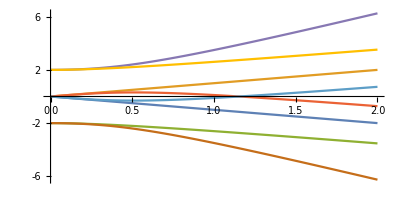

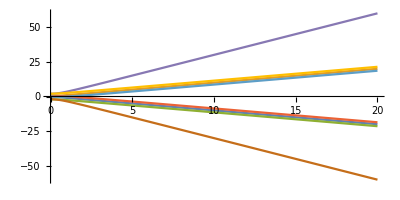

```mathematica
Plot[{-g,g,Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,1],Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,2],Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,3],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,1],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,2],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,3]},{g,0,2},AspectRatio->0.5,Ticks->{Automatic,{-6,-4,-2,0,2,4,6}}]
Plot[{-g,g,Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,1],Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,2],Root[4 g-3 g^3+(-4-5 g^2) #1-g #1^2+#1^3&,3],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,1],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,2],Root[-4 g+3 g^3+(-4-5 g^2) #1+g #1^2+#1^3&,3]},{g,0,20},AspectRatio->0.5]
```

```mathematica
J=.;
g=.;
Eigenvalues[AF[-J s[1]⊗s[1]⊗𝕀⊗𝕀-J 𝕀⊗s[1]⊗s[1]⊗𝕀-J 𝕀⊗𝕀⊗s[1]⊗s[1]-J g s[3]⊗𝕀⊗𝕀⊗𝕀-J g 𝕀⊗s[3]⊗𝕀⊗𝕀-J g 𝕀⊗𝕀⊗s[3]⊗𝕀-J g 𝕀⊗𝕀⊗𝕀⊗s[3]]]
```

(-J
J
-J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1]
J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1]
-J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2]
J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2]
-J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3]
J √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3]
J Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,1]
J Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,2]
J Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,3]
J Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,4]
J Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,1]
J Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,2]
J Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,3]
J Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,4])

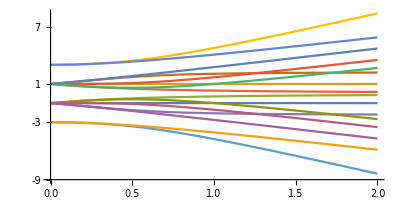

Fig3.eps

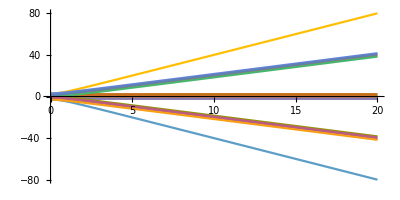

```mathematica
Plot[{-1,1,-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],- √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,1],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,2],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,4],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,1],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,2],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,3],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,4]},{g,0,2},AspectRatio->0.5,Ticks->{Automatic,{-9,-7,-5,-3,-1,0,1,3,5,7,9}},AxesOrigin->{0,-9}]
Export["Fig3.eps",Plot[{-1,1,-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],- √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,1],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,2],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,4],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,1],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,2],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,3],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,4]},{g,0,1},AspectRatio->0.5,Ticks->{Automatic,{-5,-4,-3,-2,-1,0,1,2,3,4,5}},AxesOrigin->{0,-5}]]
Plot[{-1,1,-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,1],- √Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,2],-√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],√Root[-9+(19+80 g^2) #1+(-11-16 g^2) #1^2+#1^3&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,1],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,2],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,3],Root[3+16 g^4+(2+8 g^2) #1+(-4-8 g^2) #1^2-2 #1^3+#1^4&,4],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,1],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,2],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,3],Root[3+16 g^4+(-2-8 g^2) #1+(-4-8 g^2) #1^2+2 #1^3+#1^4&,4]},{g,0,20},AspectRatio->0.5]
```

### Phase estimation for finding the spectral function; CBQC; N=2; Exact

```mathematica
(* Setup for parameters *)
Nc=2;
g=0.2;
dw=0.01;
η=0.02;
l0=1100;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1276

0.0844246

0.084548

-6.38

6.38

139

1139

(n1,n2)=(0,0)

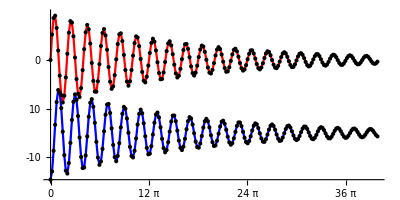

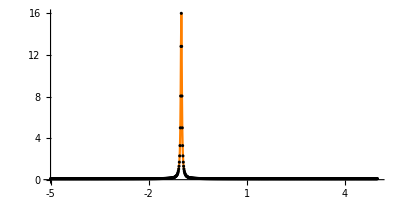

(n1,n2)=(0,1)

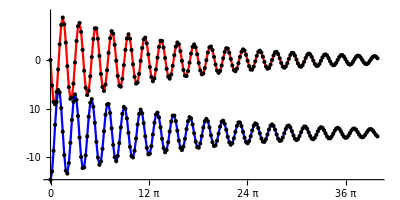

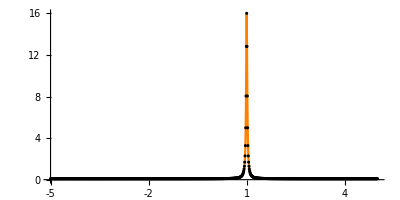

(n1,n2)=(1,0)

-Graphics-

-Graphics-

(n1,n2)=(1,1)

-Graphics-

-Graphics-

```mathematica
(* Loop for input-state choice *)
Do[
(* Build up the input ket vector *)
KetIn=AF[KetX[i1]⊗KetX[i2]];
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print["(n1,n2)=(",i1,",",i2,")"];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/5]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/5]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,4Pi,8Pi,12Pi,16Pi,20Pi,24Pi,28Pi,32Pi,36Pi,40Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]
],{i1,0,1},{i2,0,1}]
```

### Phase estimation for finding the spectral function; CBQC; N=3; Exact

```mathematica
(* Setup for parameters *)
Nc=3;
g=0.2;
dw=0.01;
η=0.02;
l0=1050;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1114

0.0950969

0.095259

-5.57

5.57

58

1058

(n1,n2,n3)=(0,0,0)

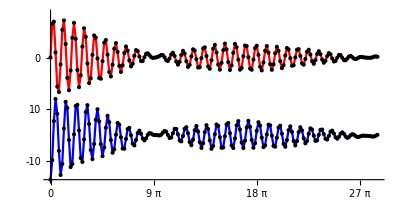

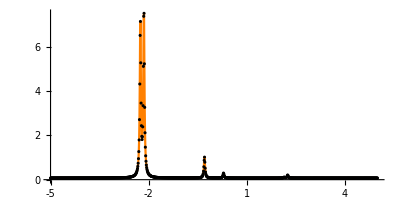

(n1,n2,n3)=(0,0,1)

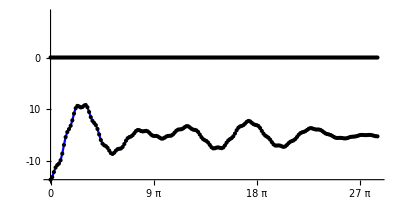

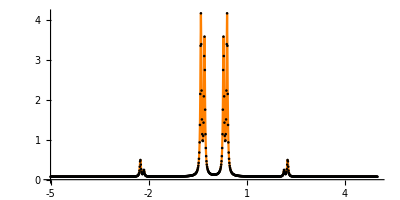

(n1,n2,n3)=(0,1,0)

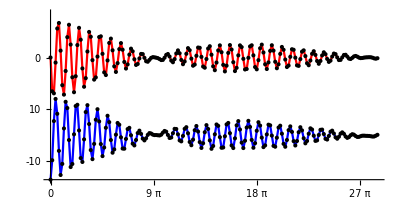

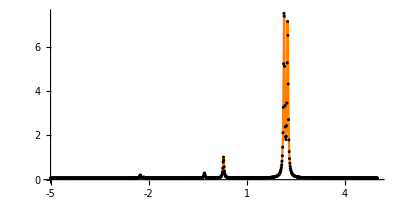

(n1,n2,n3)=(0,1,1)

-Graphics-

-Graphics-

(n1,n2,n3)=(1,0,0)

-Graphics-

-Graphics-

(n1,n2,n3)=(1,0,1)

-Graphics-

-Graphics-

(n1,n2,n3)=(1,1,0)

-Graphics-

-Graphics-

(n1,n2,n3)=(1,1,1)

-Graphics-

-Graphics-

```mathematica
(* Loop for input-state choice *)
Do[
(* Build up the input ket vector *)
KetIn=AF[KetX[i1]⊗KetX[i2]⊗KetX[i3]];
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print["(n1,n2,n3)=(",i1,",",i2,",",i3,")"];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/7]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/7]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,3Pi,6Pi,9Pi,12Pi,15Pi,18Pi,21Pi,24Pi,27Pi,30Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]
],{i1,0,1},{i2,0,1},{i3,0,1}]
```

### Phase estimation for finding the spectral function; CBQC; N=4; Exact

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.2;
dw=0.01;
η=0.02;
l0=1050;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1098

0.0921017

0.0922688

-5.49

5.49

50

1050

(n1,n2,n3,n4)=(0,0,0,0)

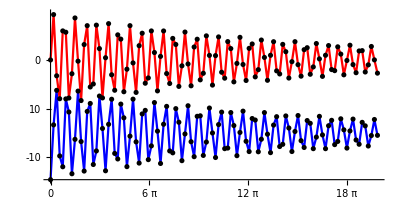

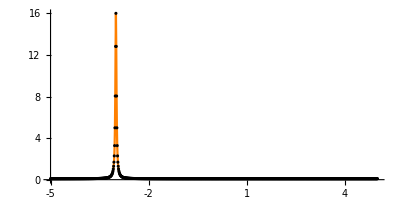

(n1,n2,n3,n4)=(0,0,0,1)

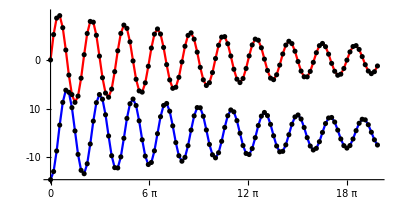

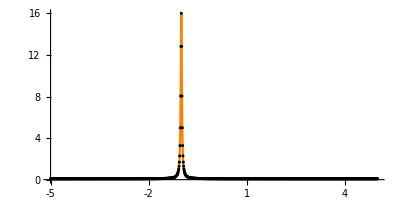

(n1,n2,n3,n4)=(0,0,1,0)

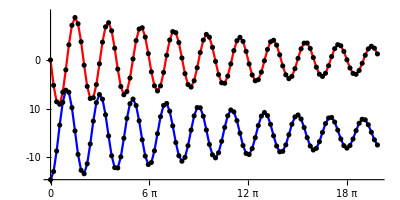

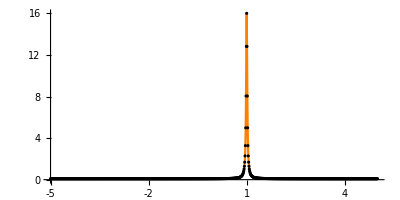

(n1,n2,n3,n4)=(0,0,1,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(0,1,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(0,1,0,1)

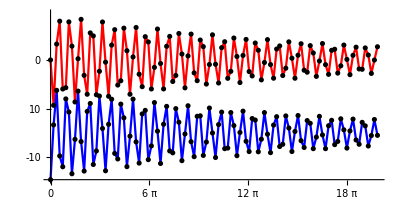

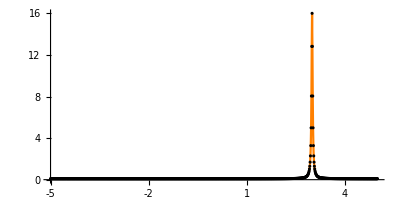

(n1,n2,n3,n4)=(0,1,1,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(0,1,1,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,0,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,1,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,1,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,0,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,1,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,1,1)

-Graphics-

-Graphics-

```mathematica
(* Loop for input-state choice *)
Do[
(* Build up the input ket vector *)
KetIn=AF[KetX[i1]⊗KetX[i2]⊗KetX[i3]⊗KetX[i4]];
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print["(n1,n2,n3,n4)=(",i1,",",i2,",",i3,",",i4,")"];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/10]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/10]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,2Pi,4Pi,6Pi,8Pi,10Pi,12Pi,14Pi,16Pi,18Pi,20Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]
],{i1,0,1},{i2,0,1},{i3,0,1},{i4,0,1}]
```

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1200;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1272

0.0799753

0.0800997

-6.36

6.36

137

1137

(n1,n2,n3,n4)=(0,0,0,0)

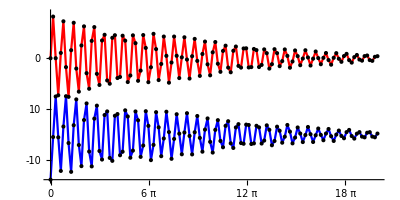

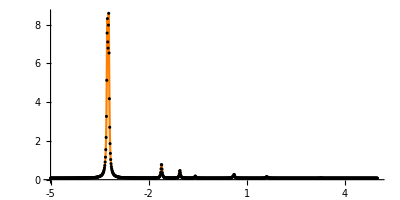

(n1,n2,n3,n4)=(0,0,0,1)

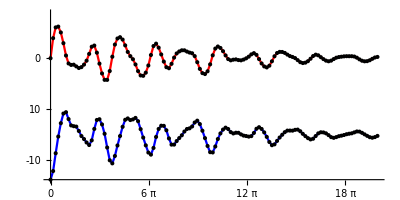

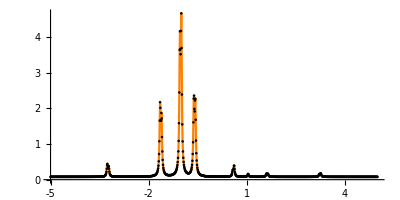

(n1,n2,n3,n4)=(0,0,1,0)

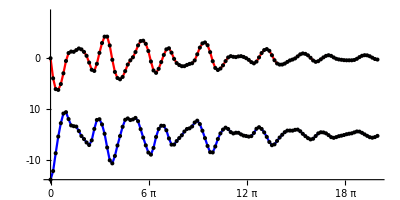

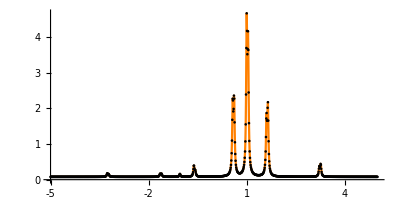

(n1,n2,n3,n4)=(0,0,1,1)

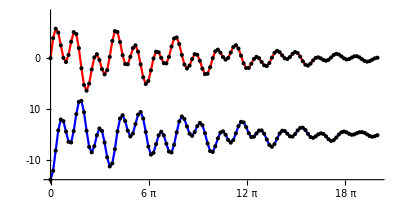

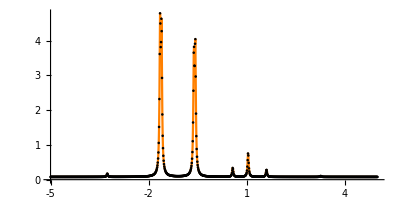

(n1,n2,n3,n4)=(0,1,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(0,1,0,1)

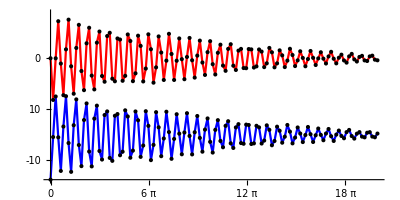

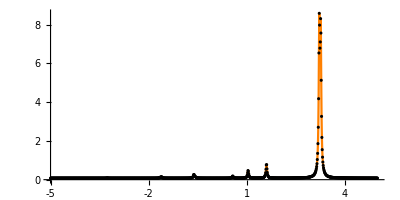

(n1,n2,n3,n4)=(0,1,1,0)

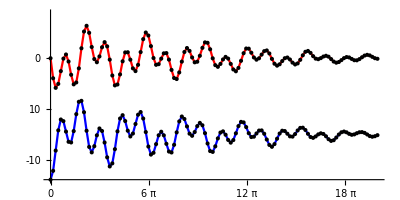

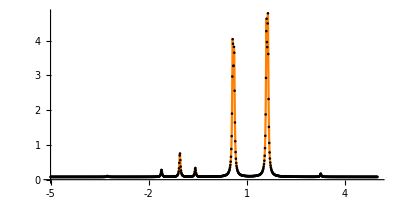

(n1,n2,n3,n4)=(0,1,1,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,0,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,1,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,0,1,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,0,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,0,1)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,1,0)

-Graphics-

-Graphics-

(n1,n2,n3,n4)=(1,1,1,1)

-Graphics-

-Graphics-

```mathematica
(* Loop for input-state choice *)
Do[
(* Build up the input ket vector *)
KetIn=AF[KetX[i1]⊗KetX[i2]⊗KetX[i3]⊗KetX[i4]];
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print["(n1,n2,n3,n4)=(",i1,",",i2,",",i3,",",i4,")"];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/10]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/10]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,2Pi,4Pi,6Pi,8Pi,10Pi,12Pi,14Pi,16Pi,18Pi,20Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]
],{i1,0,1},{i2,0,1},{i3,0,1},{i4,0,1}]
```

## Fourier sampling test 1

### Data 1

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1266;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L1=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L1]
Print[SpectralFunction[[L1/2+1]]]
Print[SpectralFunction0[[L1/2]]]
Print[(1-(L1/2+1))dw]
Print[(L1+1-(L1/2+1))dw]
Print[Floor[L1/2+1-5/dw]]
Print[Ceiling[L1/2+1+5/dw]]
```

1272

0.0799753

0.0800997

-6.36

6.36

137

1137

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction1=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L1*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L1*dw)√L1)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L1}];
(* Fourier transform *)
SpectralFunction1=-1/Pi Im[Fourier[OverlapFunction1]];
SpectralFunction1=Table[If[k≤L1/2,SpectralFunction1[[k+L1/2]],SpectralFunction1[[k-L1/2]]],{k,1,L1+1}];
```

### Data 2

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=970;
TolF=0.0003;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L2=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L2]
Print[SpectralFunction[[L2/2+1]]]
Print[SpectralFunction0[[L2/2]]]
Print[(1-(L2/2+1))dw]
Print[(L+1-(L2/2+1))dw]
Print[Floor[L2/2+1-5/dw]]
Print[Ceiling[L2/2+1+5/dw]]
```

976

0.103944

0.104156

-4.88

-2.48

-11

989

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction2=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L2*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L2*dw)√L2)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L2}];
(* Fourier transform *)
SpectralFunction2=-1/Pi Im[Fourier[OverlapFunction2]];
SpectralFunction2=Table[If[k≤L2/2,SpectralFunction2[[k+L2/2]],SpectralFunction2[[k-L2/2]]],{k,1,L2+1}];
```

### Data 3

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=680;
TolF=0.001;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L3=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L3]
Print[SpectralFunction[[L3/2+1]]]
Print[SpectralFunction0[[L3/2]]]
Print[(1-(L3/2+1))dw]
Print[(L3+1-(L3/2+1))dw]
Print[Floor[L3/2+1-5/dw]]
Print[Ceiling[L3/2+1+5/dw]]
```

714

0.1419

0.142299

-3.57

3.57

-142

858

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction3=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L3*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L3*dw)√L3)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L3}];
(* Fourier transform *)
SpectralFunction3=-1/Pi Im[Fourier[OverlapFunction3]];
SpectralFunction3=Table[If[k≤L3/2,SpectralFunction3[[k+L3/2]],SpectralFunction3[[k-L3/2]]],{k,1,L3+1}];
```

### Data 4

```mathematica
(* Fourier sampling size *)
L4=460;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction4=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L4*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L4*dw)√L4)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L4}];
(* Print the result *)
SpectralFunction4=-1/Pi Im[Fourier[OverlapFunction4]];
SpectralFunction4=Table[If[k≤L4/2,SpectralFunction4[[k+L4/2]],SpectralFunction4[[k-L4/2]]],{k,1,L4+1}];
```

### Data 5

```mathematica
(* Fourier sampling size *)
L5=260;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction5=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L5*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L5*dw)√L5)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L5}];
(* Print the result *)
SpectralFunction5=-1/Pi Im[Fourier[OverlapFunction5]];
SpectralFunction5=Table[If[k≤L5/2,SpectralFunction4[[k+L5/2]],SpectralFunction4[[k-L5/2]]],{k,1,L5+1}];
```

### Data 6

```mathematica
(* Fourier sampling size *)
L6=160;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction6=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L6*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L6*dw)√L6)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L6}];
(* Print the result *)
SpectralFunction6=-1/Pi Im[Fourier[OverlapFunction6]];
SpectralFunction6=Table[If[k≤L6/2,SpectralFunction4[[k+L6/2]],SpectralFunction4[[k-L6/2]]],{k,1,L6+1}];
```

### Plots

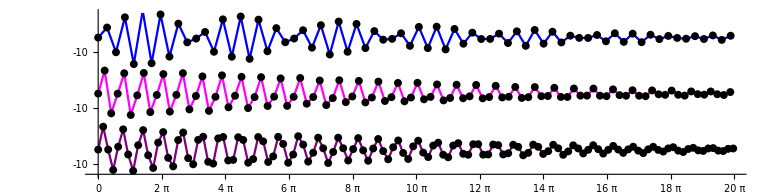

```mathematica
Data1=Table[{(j-1)(2Pi)/(L1*dw),Re[OverlapFunction1[[j]]]},{j,1,Ceiling[L1/10]}];
Data2=Table[{(j-1)(2Pi)/(L2*dw),Re[OverlapFunction2[[j]]]+40},{j,1,Ceiling[L2/10]}];
Data3=Table[{(j-1)(2Pi)/(L3*dw),Re[OverlapFunction3[[j]]]+80},{j,1,Ceiling[L3/10]}];
Print[ListPlot[{Data1,Data2,Data3},
AxesOrigin->{0,Im[OverlapFunction1[[1]]]},PlotRange->{Im[OverlapFunction1[[1]]],80-Im[OverlapFunction1[[1]]]},Joined->True,PlotStyle->{Purple,Magenta,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.25,Ticks->{{0,2Pi,4Pi,6Pi,8Pi,10Pi,12Pi,14Pi,16Pi,18Pi,20Pi},{-10,0,10,{30,"-10"},{40,"0"},{50,"10"},{70,"-10"},{80,"0"},{90,"10"}}}]]
```

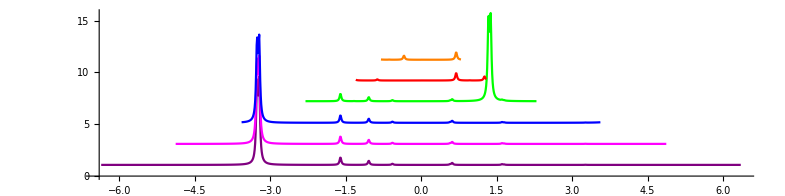

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]+1},{j,0,L1}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]+3},{j,0,L2}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]+5},{j,0,L3}];
Data4=Table[{(j-(L4/2+1))dw,SpectralFunction4[[j]]+7},{j,0,L4}];
Data5=Table[{(j-(L5/2+1))dw,SpectralFunction5[[j]]+9},{j,0,L5}];
Data6=Table[{(j-(L6/2+1))dw,SpectralFunction6[[j]]+11},{j,0,L6}];
Print[ListPlot[{Data1,Data2,Data3,Data4,Data5,Data6},AxesOrigin->{-6.4,0},Joined->True,PlotStyle->{Purple,Magenta,Blue,Green,Red,Orange},Mesh->None,MeshStyle->Black,PlotRange->All,AspectRatio->0.25]]
```

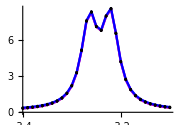

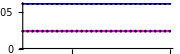

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-3.4/dw],Floor[L1/2+1-3.1/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1-3.4/dw],Floor[L2/2+1-3.1/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1-3.4/dw],Floor[L3/2+1-3.1/dw]}];
DataDev1and2=Table[{(j-(L1/2+1))dw,SpectralFunction2[[j-(L1-L2)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-3.4/dw],Floor[L1/2+1-3.1/dw]}];
DataDev1and3=Table[{(j-(L1/2+1))dw,SpectralFunction3[[j-(L1-L3)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-3.4/dw],Floor[L1/2+1-3.1/dw]}];
Print[ListPlot[{Data1,Data2,Data3},AxesOrigin->{-3.4,0},Joined->True,PlotStyle->{Purple,Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.7,Ticks->{{-3.4,-3.3,-3.2,-3.1},Automatic}]];
Print[ListPlot[{DataDev1and2,DataDev1and3},AxesOrigin->{-3.4,0},Joined->True,PlotStyle->{Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.3,Ticks->{{-3.3,-3.2,-3.1},{0,0.05}}]]
```

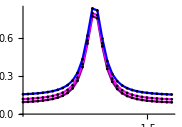

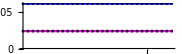

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.75/dw],Floor[L1/2+1-1.45/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1-1.75/dw],Floor[L2/2+1-1.45/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1-1.75/dw],Floor[L3/2+1-1.45/dw]}];
DataDev1and2=Table[{(j-(L1/2+1))dw,SpectralFunction2[[j-(L1-L2)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.75/dw],Floor[L1/2+1-1.45/dw]}];
DataDev1and3=Table[{(j-(L1/2+1))dw,SpectralFunction3[[j-(L1-L3)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.75/dw],Floor[L1/2+1-1.45/dw]}];
Print[ListPlot[{Data1,Data2,Data3},AxesOrigin->{-1.75,0},Joined->True,PlotStyle->{Purple,Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.7,Ticks->{{-1.8,-1.7,-1.6,-1.5,-1.4},Automatic}]];
Print[ListPlot[{DataDev1and2,DataDev1and3},AxesOrigin->{-1.75,0},Joined->True,PlotStyle->{Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.3,Ticks->{{-1.8,-1.7,-1.6,-1.5,-1.4},{0,0.05}}]]
```

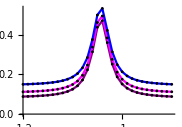

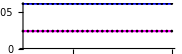

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.2/dw],Floor[L1/2+1-0.9/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1-1.2/dw],Floor[L2/2+1-0.9/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1-1.2/dw],Floor[L3/2+1-0.9/dw]}];
DataDev1and2=Table[{(j-(L1/2+1))dw,SpectralFunction2[[j-(L1-L2)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.2/dw],Floor[L1/2+1-0.9/dw]}];
DataDev1and3=Table[{(j-(L1/2+1))dw,SpectralFunction3[[j-(L1-L3)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-1.2/dw],Floor[L1/2+1-0.9/dw]}];
Print[ListPlot[{Data1,Data2,Data3},AxesOrigin->{-1.2,0},Joined->True,PlotStyle->{Purple,Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.7,Ticks->{{-1.2,-1.1,-1,-0.9},Automatic}]];
Print[ListPlot[{DataDev1and2,DataDev1and3},AxesOrigin->{-1.2,0},Joined->True,PlotStyle->{Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.3,Ticks->{{-1.1,-1,-0.9},{0,0.05}}]]
```

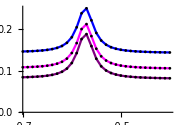

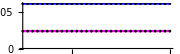

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-0.7/dw],Floor[L1/2+1-0.4/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1-0.7/dw],Floor[L2/2+1-0.4/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1-0.7/dw],Floor[L3/2+1-0.4/dw]}];
DataDev1and2=Table[{(j-(L1/2+1))dw,SpectralFunction2[[j-(L1-L2)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-0.7/dw],Floor[L1/2+1-0.4/dw]}];
DataDev1and3=Table[{(j-(L1/2+1))dw,SpectralFunction3[[j-(L1-L3)/2]]-SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-0.7/dw],Floor[L1/2+1-0.4/dw]}];
Print[ListPlot[{Data1,Data2,Data3},AxesOrigin->{-0.7,0},Joined->True,PlotStyle->{Purple,Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.7,Ticks->{{-0.7,-0.6,-0.5,-0.4},Automatic}]];
Print[ListPlot[{DataDev1and2,DataDev1and3},AxesOrigin->{-0.7,0},Joined->True,PlotStyle->{Magenta,Blue},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.3,Ticks->{{-0.6,-0.5,-0.4},{0,0.05}}]]
```

## Fourier sampling test 2

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1266;
TolF=0.0002;
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L1=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L1]
Print[SpectralFunction[[L1/2+1]]]
Print[SpectralFunction0[[L1/2]]]
Print[(1-(L1/2+1))dw]
Print[(L1+1-(L1/2+1))dw]
Print[Floor[L1/2+1-5/dw]]
Print[Ceiling[L1/2+1+5/dw]]
```

```mathematica
L1=1000;
L2=820;
L3=600;
L4=440;
L5=340;
L6=160;
```

### Data 1

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction1=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L1*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L1*dw)√L1)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L1}];
(* Fourier transform *)
SpectralFunction1=-1/Pi Im[Fourier[OverlapFunction1]];
SpectralFunction1=Table[If[k≤L1/2,SpectralFunction1[[k+L1/2]],SpectralFunction1[[k-L1/2]]],{k,1,L1+1}];
```

### Data 2

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction2=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L2*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L2*dw)√L2)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L2}];
(* Fourier transform *)
SpectralFunction2=-1/Pi Im[Fourier[OverlapFunction2]];
SpectralFunction2=Table[If[k≤L2/2,SpectralFunction2[[k+L2/2]],SpectralFunction2[[k-L2/2]]],{k,1,L2+1}];
```

### Data 3

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction3=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L3*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L3*dw)√L3)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L3}];
(* Fourier transform *)
SpectralFunction3=-1/Pi Im[Fourier[OverlapFunction3]];
SpectralFunction3=Table[If[k≤L3/2,SpectralFunction3[[k+L3/2]],SpectralFunction3[[k-L3/2]]],{k,1,L3+1}];
```

### Data 4

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction4=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L4*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L4*dw)√L4)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L4}];
(* Print the result *)
SpectralFunction4=-1/Pi Im[Fourier[OverlapFunction4]];
SpectralFunction4=Table[If[k≤L4/2,SpectralFunction4[[k+L4/2]],SpectralFunction4[[k-L4/2]]],{k,1,L4+1}];
```

### Data 5

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction5=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L5*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L5*dw)√L5)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L5}];
(* Print the result *)
SpectralFunction5=-1/Pi Im[Fourier[OverlapFunction5]];
SpectralFunction5=Table[If[k≤L5/2,SpectralFunction5[[k+L5/2]],SpectralFunction5[[k-L5/2]]],{k,1,L5+1}];
```

### Data 6

```mathematica
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for time variable *)
OverlapFunction6=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L6*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L6*dw)√L6)I Exp[-η ϕ]Exp[-I 3ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L6}];
(* Print the result *)
SpectralFunction6=-1/Pi Im[Fourier[OverlapFunction6]];
SpectralFunction6=Table[If[k≤L6/2,SpectralFunction6[[k+L6/2]],SpectralFunction6[[k-L6/2]]],{k,1,L6+1}];
```

### Plots

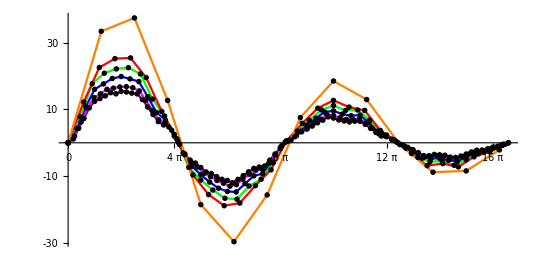

```mathematica
Data1=Table[{(j-1)(2Pi)/(L1*dw),Re[OverlapFunction1[[j]]]},{j,1,Ceiling[L1/12]}];
Data2=Table[{(j-1)(2Pi)/(L2*dw),Re[OverlapFunction2[[j]]]},{j,1,Ceiling[L2/12]}];
Data3=Table[{(j-1)(2Pi)/(L3*dw),Re[OverlapFunction3[[j]]]},{j,1,Ceiling[L3/12]}];
Data4=Table[{(j-1)(2Pi)/(L4*dw),Re[OverlapFunction4[[j]]]},{j,1,Ceiling[L4/12]}];
Data5=Table[{(j-1)(2Pi)/(L5*dw),Re[OverlapFunction5[[j]]]},{j,1,Ceiling[L5/12]}];
Data6=Table[{(j-1)(2Pi)/(L6*dw),Re[OverlapFunction6[[j]]]},{j,1,Ceiling[L6/12]}];
Print[ListPlot[{Data1,Data2,Data3,Data4,Data5,Data6},
AxesOrigin->{0,0},PlotRange->All,Joined->True,PlotStyle->{Purple,Magenta,Blue,Green,Red,Orange},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,2Pi,4Pi,6Pi,8Pi,10Pi,12Pi,14Pi,16Pi,18Pi,20Pi},{-30,-20,-10,0,10,20,30,40}}]]
```

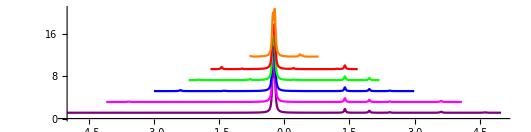

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]+1},{j,0,L1}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]+3},{j,0,L2}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]+5},{j,0,L3}];
Data4=Table[{(j-(L4/2+1))dw,SpectralFunction4[[j]]+7},{j,0,L4}];
Data5=Table[{(j-(L5/2+1))dw,SpectralFunction5[[j]]+9},{j,0,L5}];
Data6=Table[{(j-(L6/2+1))dw,SpectralFunction6[[j]]+11},{j,0,L6}];
Print[ListPlot[{Data1,Data2,Data3,Data4,Data5,Data6},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Purple,Magenta,Blue,Green,Red,Orange},Mesh->None,MeshStyle->Black,PlotRange->All,AspectRatio->0.25]]
```

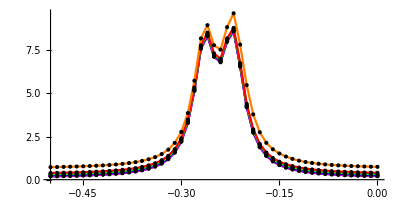

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1-0.5/dw],Floor[L1/2+1+0/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1-0.5/dw],Floor[L2/2+1+0/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1-0.5/dw],Floor[L3/2+1+0/dw]}];
Data4=Table[{(j-(L4/2+1))dw,SpectralFunction4[[j]]},{j,Ceiling[L4/2+1-0.5/dw],Floor[L4/2+1+0/dw]}];
Data5=Table[{(j-(L5/2+1))dw,SpectralFunction5[[j]]},{j,Ceiling[L5/2+1-0.5/dw],Floor[L5/2+1+0/dw]}];
Data6=Table[{(j-(L6/2+1))dw,SpectralFunction6[[j]]},{j,Ceiling[L6/2+1-0.5/dw],Floor[L6/2+1+0/dw]}];
Print[ListPlot[{Data1,Data2,Data3,Data4,Data5,Data6},AxesOrigin->{-0.5,0},Joined->True,PlotStyle->{Purple,Magenta,Blue,Green,Red,Orange},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5]]
```

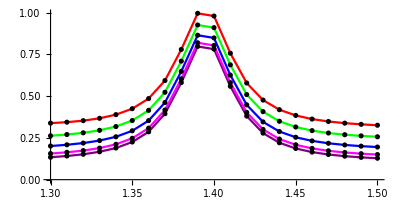

```mathematica
Data1=Table[{(j-(L1/2+1))dw,SpectralFunction1[[j]]},{j,Ceiling[L1/2+1+1.3/dw],Floor[L1/2+1+1.5/dw]}];
Data2=Table[{(j-(L2/2+1))dw,SpectralFunction2[[j]]},{j,Ceiling[L2/2+1+1.3/dw],Floor[L2/2+1+1.5/dw]}];
Data3=Table[{(j-(L3/2+1))dw,SpectralFunction3[[j]]},{j,Ceiling[L3/2+1+1.3/dw],Floor[L3/2+1+1.5/dw]}];
Data4=Table[{(j-(L4/2+1))dw,SpectralFunction4[[j]]},{j,Ceiling[L4/2+1+1.3/dw],Floor[L4/2+1+1.5/dw]}];
Data5=Table[{(j-(L5/2+1))dw,SpectralFunction5[[j]]},{j,Ceiling[L5/2+1+1.3/dw],Floor[L5/2+1+1.5/dw]}];
Print[ListPlot[{Data1,Data2,Data3,Data4,Data5},AxesOrigin->{1.3,0},Joined->True,PlotStyle->{Purple,Magenta,Blue,Green,Red},Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5]]
```

## Error analysis with random input

### N=2

```mathematica
(* Setup for parameters *)
Nc=2;
g=0.4;
dw=0.01;
η=0.02;
l0=1400;
TolF=0.0002;
(* Random generation of qubit rotation operator *)
θ1=RandomReal[{0,Pi}];
φ1=RandomReal[{0,2Pi}];
α1=RandomReal[{0,0.1*2Pi}];
RotGen1=Cos[-α1/2]𝕀+I Sin[-α1/2](Sin[θ1]Cos[φ1]s[1]+Sin[θ1]Sin[φ1]s[2]+Cos[θ1]s[3]);
θ2=RandomReal[{0,Pi}];
φ2=RandomReal[{0,2Pi}];
α2=RandomReal[{0,0.1*2Pi}];
RotGen2=Cos[-α2/2]𝕀+I Sin[-α2/2](Sin[θ2]Cos[φ2]s[1]+Sin[θ2]Sin[φ2]s[2]+Cos[θ2]s[3]);
(* Build up the input ket vector *)
Print["(θ1,φ1,α1)=(",θ1/Pi,"π,",φ1/Pi,"π,",α1/Pi,"π)"]
Print["(θ2,φ2,α2)=(",θ2/Pi,"π,",φ2/Pi,"π,",α2/Pi,"π)"]
KetIn=AF[(RotGen1.KetX[0])⊗(RotGen2.KetX[0])]
```

(θ1,φ1,α1)=(0.99607π,0.27952π,0.0461208π)

(θ2,φ2,α2)=(0.527421π,0.568447π,0.018714π)

(0.483557+0.0392348 ⅈ
0.512252+0.0387686 ⅈ
0.48486-0.0310348 ⅈ
0.513229-0.0356457 ⅈ)

```mathematica
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1426

0.0753546

0.0754534

-7.13

7.13

214

1214

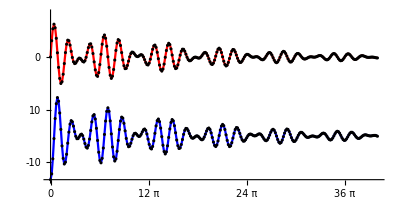

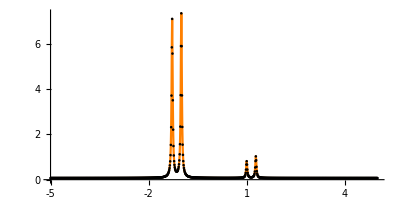

```mathematica
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/5]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/5]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,4Pi,8Pi,12Pi,16Pi,20Pi,24Pi,28Pi,32Pi,36Pi,40Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

### N=3

```mathematica
(* Setup for parameters *)
Nc=3;
g=0.4;
dw=0.01;
η=0.02;
l0=1300;
TolF=0.0002;
(* Random generation of qubit rotation operator *)
θ1=RandomReal[{0,Pi}];
φ1=RandomReal[{0,2Pi}];
α1=RandomReal[{0,0.1*2Pi}];
RotGen1=Cos[-α1/2]𝕀+I Sin[-α1/2](Sin[θ1]Cos[φ1]s[1]+Sin[θ1]Sin[φ1]s[2]+Cos[θ1]s[3]);
θ2=RandomReal[{0,Pi}];
φ2=RandomReal[{0,2Pi}];
α2=RandomReal[{0,0.1*2Pi}];
RotGen2=Cos[-α2/2]𝕀+I Sin[-α2/2](Sin[θ2]Cos[φ2]s[1]+Sin[θ2]Sin[φ2]s[2]+Cos[θ2]s[3]);
θ3=RandomReal[{0,Pi}];
φ3=RandomReal[{0,2Pi}];
α3=RandomReal[{0,0.1*2Pi}];
RotGen3=Cos[-α3/2]𝕀+I Sin[-α3/2](Sin[θ3]Cos[φ3]s[1]+Sin[θ3]Sin[φ3]s[2]+Cos[θ3]s[3]);
(* Build up the input ket vector *)
Print["(θ1,φ1,α1)=(",θ1/Pi,"π,",φ1/Pi,"π,",α1/Pi,"π)"]
Print["(θ2,φ2,α2)=(",θ2/Pi,"π,",φ2/Pi,"π,",α2/Pi,"π)"]
Print["(θ3,φ3,α3)=(",θ3/Pi,"π,",φ3/Pi,"π,",α3/Pi,"π)"]
KetIn=AF[(RotGen1.KetX[0])⊗(RotGen2.KetX[0])⊗(RotGen3.KetX[0])]
```

(θ1,φ1,α1)=(0.464341π,0.433654π,0.00929434π)

(θ2,φ2,α2)=(0.709629π,1.32189π,0.162809π)

(θ3,φ3,α3)=(0.565449π,0.411754π,0.159037π)

(0.293432+0.0593378 ⅈ
0.4871+0.0607717 ⅈ
0.204368-0.0178174 ⅈ
0.331947-0.0543774 ⅈ
0.301673+0.0620571 ⅈ
0.500911+0.0641998 ⅈ
0.210312-0.0176259 ⅈ
0.341689-0.0547984 ⅈ)

```mathematica
(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1504

0.0819601

0.0820489

-7.52

7.52

253

1253

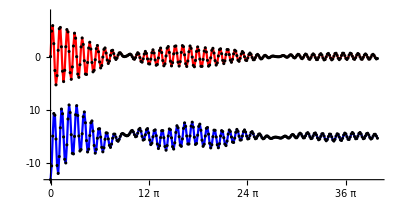

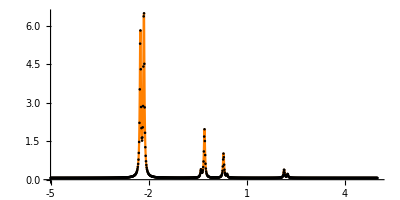

```mathematica
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
Print[ListPlot[{Table[{(j-1)(2Pi)/(L*dw),Re[OverlapFunction[[j]]]+30},{j,1,Ceiling[L/5]}],Table[{(j-1)(2Pi)/(L*dw),Im[OverlapFunction[[j]]]},{j,1,Ceiling[L/5]}]},
AxesOrigin->{0,Im[OverlapFunction[[1]]]},PlotRange->{Im[OverlapFunction[[1]]],30-Im[OverlapFunction[[1]]]},Joined->True,PlotStyle->{Red,Blue},Mesh->All,MeshStyle->Black,AspectRatio->0.5,Ticks->{{0,4Pi,8Pi,12Pi,16Pi,20Pi,24Pi,28Pi,32Pi,36Pi,40Pi},{-10,0,10,{20,"-10"},{30,"0"},{40,"10"}}}]];
Print[ListPlot[Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}],AxesOrigin->{-5,0},Joined->True,PlotStyle->Orange,Mesh->All,MeshStyle->Black,PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

### N=4 (random rotation around z axis)

```mathematica
(* Random generation of qubit rotation angle *)
KetIn0=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
```

```mathematica
(* Random generation of qubit rotation angle *)
n=1;(* 1,2 *)
α1=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α2=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α3=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α4=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
(* Build up the input ket vector *)
KetIn0=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
KetIn=AF[(RotZ[α1].KetX[0])⊗(RotZ[α2].KetX[0])⊗(RotZ[α3].KetX[0])⊗(RotZ[α4].KetX[0])];
Print["(α1,α2,α3,α4)=(",α1/Pi,"π,",α2/Pi,"π,",α3/Pi,"π,",α4/Pi,"π)"]
```

(α1,α2,α3,α4)=(0.210586π,0.203315π,0.211591π,0.258851π)

```mathematica
(* Random generation of qubit rotation angle *)
n=2;(* 1,2 *)
α1=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α2=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α3=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α4=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
(* Build up the input ket vector *)
KetIn0=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
KetIn=AF[(RotZ[α1].KetX[0])⊗(RotZ[α2].KetX[0])⊗(RotZ[α3].KetX[0])⊗(RotZ[α4].KetX[0])];
Print["(α1,α2,α3,α4)=(",α1/Pi,"π,",α2/Pi,"π,",α3/Pi,"π,",α4/Pi,"π)"]
```

(α1,α2,α3,α4)=(0.385761π,0.488477π,0.475736π,0.356728π)

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1850;
TolF=0.0002;

(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn0)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1852

-0.00957275

-0.00954799

-9.26

9.26

427

1427

```mathematica
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn0)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunctionRe=-1/Pi Re[Fourier[OverlapFunction]];
SpectralFunctionRe=Table[If[k≤L/2,SpectralFunctionRe[[k+L/2]],SpectralFunctionRe[[k-L/2]]],{k,1,L+1}];
SpectralFunctionIm=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunctionIm=Table[If[k≤L/2,SpectralFunctionIm[[k+L/2]],SpectralFunctionIm[[k-L/2]]],{k,1,L+1}];
LRe3=Table[{(j-(L/2+1))dw,SpectralFunctionRe[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}];
LIm3=Table[{(j-(L/2+1))dw,SpectralFunctionIm[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}];
```

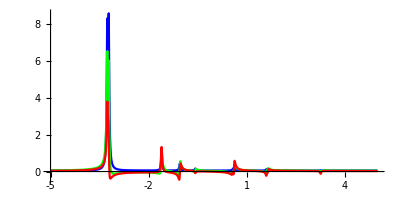

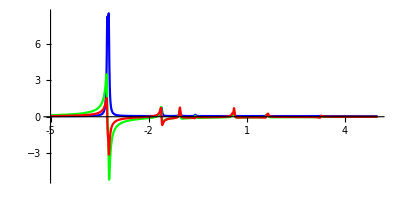

```mathematica
Print[ListPlot[{LIm1,LIm2,LIm3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
Print[ListPlot[{LIm1,LRe2,LRe3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

```mathematica
Export["Fig3.eps",ListPlot[{L1,L2,L3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

Fig3.eps

### N=4 (random rotation around y axis)

```mathematica
(* Random generation of qubit rotation angle *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
```

```mathematica
(* Random generation of qubit rotation angle *)
n=1;(* 1,2 *)
α1=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α2=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α3=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α4=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
(* Build up the input ket vector *)
KetIn=AF[(RotY[α1].KetX[0])⊗(RotY[α2].KetX[0])⊗(RotY[α3].KetX[0])⊗(RotY[α4].KetX[0])];
Print["(α1,α2,α3,α4)=(",α1/Pi,"π,",α2/Pi,"π,",α3/Pi,"π,",α4/Pi,"π)"]
```

(α1,α2,α3,α4)=(0.210393π,0.22215π,0.288532π,0.228578π)

```mathematica
(* Random generation of qubit rotation angle *)
n=2;(* 1,2 *)
α1=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α2=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α3=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
α4=RandomReal[{n/3 Pi/2,(n+1)/3 Pi/2}];
(* Build up the input ket vector *)
KetIn=AF[(RotY[α1].KetX[0])⊗(RotY[α2].KetX[0])⊗(RotY[α3].KetX[0])⊗(RotY[α4].KetX[0])];
Print["(α1,α2,α3,α4)=(",α1/Pi,"π,",α2/Pi,"π,",α3/Pi,"π,",α4/Pi,"π)"]
```

(α1,α2,α3,α4)=(0.360979π,0.454048π,0.434987π,0.463969π)

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1850;
TolF=0.0002;

(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1852

0.0591202

0.0591787

-9.26

9.26

427

1427

```mathematica
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
L3=Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}];
```

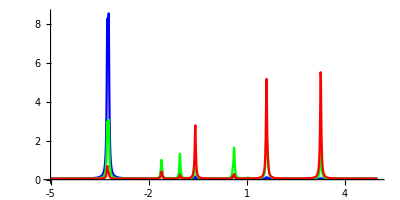

```mathematica
Print[ListPlot[{L1,L2,L3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

```mathematica
Export["Fig3.eps",ListPlot[{L1,L2,L3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

### N=4 (random rotation of basis change)

```mathematica
(* Setup for parameters *)
Nc=4;
g=0.4;
dw=0.01;
η=0.02;
l0=1850;
TolF=0.0002;
ϵ=0.2Pi/2;(* 0, 0.1, 0.2 *)

(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];

(* Loop for Fourier transform *)
Do[
(* Define the overlap function in time domain *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(l*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g (AF[(RotY[ϵ].s[3].RotY[-ϵ])⊗𝕀]+AF[𝕀⊗(RotY[ϵ].s[3].RotY[-ϵ])]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗(RotY[ϵ].s[3].RotY[-ϵ])]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(l*dw)√l)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],
{k,1,l}];
(* Define the spectral function *)
If[l==l0,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
SpectralFunction0=SpectralFunction,
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤l/2,SpectralFunction[[k+l/2]],SpectralFunction[[k-l/2]]],{k,1,l+1}];
Dev=√(Sum[(SpectralFunction[[k+1]]-SpectralFunction0[[k]])^2,{k,1,l-1}]/Sum[(SpectralFunction0[[k]])^2,{k,1,l-1}]);
If[Dev<TolF,
L=l;Break[],
SpectralFunction0=SpectralFunction]
],{l,l0,10^6,2}];
Print[L]
Print[SpectralFunction[[L/2+1]]]
Print[SpectralFunction0[[L/2]]]
Print[(1-(L/2+1))dw]
Print[(L+1-(L/2+1))dw]
Print[Floor[L/2+1-5/dw]]
Print[Ceiling[L/2+1+5/dw]]
```

1852

0.0550381

0.0550966

-9.26

9.26

427

1427

```mathematica
(* Loop for time variable *)
OverlapFunction=Table[
(* Define the time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(* Build up the output ket vector for the circuit model *)
Ham=AF[s[1]⊗s[1]]+g(AF[(RotY[ϵ].s[3].RotY[-ϵ])⊗𝕀]+AF[𝕀⊗(RotY[ϵ].s[3].RotY[-ϵ])]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham=AF[Ham⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗(RotY[ϵ].s[3].RotY[-ϵ])]
]];
Gate=MatrixExp[I ϕ Ham];
(* Build up the overlap function *)
Chop[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]],{k,1,L}];
(* Print the result *)
SpectralFunction=-1/Pi Im[Fourier[OverlapFunction]];
SpectralFunction=Table[If[k≤L/2,SpectralFunction[[k+L/2]],SpectralFunction[[k-L/2]]],{k,1,L+1}];
L3=Table[{(j-(L/2+1))dw,SpectralFunction[[j]]},{j,Ceiling[L/2+1-5/dw],Floor[L/2+1+5/dw]}];
```

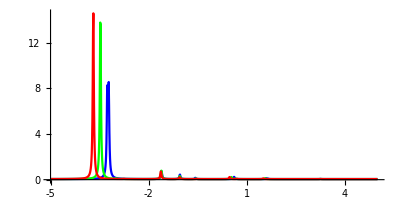

```mathematica
Print[ListPlot[{L1,L2,L3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

```mathematica
Export["Fig3.eps",ListPlot[{L1,L2,L3},AxesOrigin->{-5,0},Joined->True,PlotStyle->{Blue,Green,Red},PlotRange->All,AspectRatio->0.5,Ticks->{{-5,-4,-3,-2,-1,0,1,2,3,4,5},Automatic}]]
```

### Extra consideration

```mathematica
ϵ=.;
CPHASEerr=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, Exp[-I Pi(1+Re[ϵ])]}});
CPHASEerr.AF[s[3]⊗𝕀].Adj[CPHASEerr]
CPHASEerr.AF[s[1]⊗𝕀].Adj[CPHASEerr]
CPHASEerr.AF[(s[1]+I s[2])/2⊗𝕀].Adj[CPHASEerr]
CPHASEerr.AF[(s[1]-I s[2])/2⊗𝕀].Adj[CPHASEerr]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 0 | -1)

(0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ π (1+Re[ϵ]))
1 | 0 | 0 | 0
0 | ⅇ^(-ⅈ π (1+Re[ϵ])) | 0 | 0)

(0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(ⅈ π (1+Re[ϵ]))
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
1 | 0 | 0 | 0
0 | ⅇ^(-ⅈ π (1+Re[ϵ])) | 0 | 0)

```mathematica
ϵ=.;
CPHASEerr=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, Exp[-I Pi Re[ϵ]]}});
AF[s[1]⊗𝕀].CPHASEerr
```

(0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(-ⅈ π Re[ϵ])
1 | 0 | 0 | 0
0 | 1 | 0 | 0)

```mathematica
((s[1]+I s[2])/2).((s[1]-I s[2])/2)
```

(1 | 0
0 | 0)

```mathematica
AF[(𝕀-s[3])/2⊗(𝕀-s[3])/2]
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 1)

```mathematica
ϵ=.;
MatrixExp[-I Pi(1+ϵ)AF[(𝕀-s[3])/2⊗(𝕀-s[3])/2]]
```

(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | ⅇ^(-ⅈ π (1+ϵ)))

```mathematica
Series[Exp[-I Pi(1+x)],{x,0,1}]
```

-1+ⅈ π x+O[x]^2

## Phase estimation for finding the spectral function; CBQC; Trotter

### N=2 case

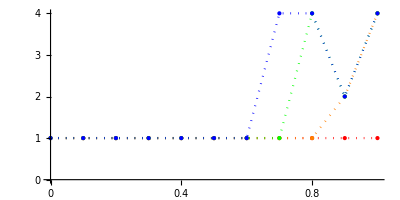

```mathematica
(* Set up parameters *)
Nc=2;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.0001];
If[i==2,g=0.0002];
If[i==3,g=0.0003];
If[i==4,g=0.0004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

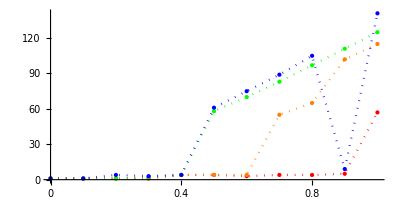

```mathematica
(* Set up parameters *)
Nc=2;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.001];
If[i==2,g=0.002];
If[i==3,g=0.003];
If[i==4,g=0.004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

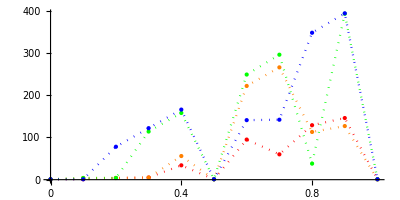

```mathematica
(* Set up parameters *)
Nc=2;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.01];
If[i==2,g=0.02];
If[i==3,g=0.03];
If[i==4,g=0.04];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

```mathematica
(* Set up parameters *)
Nc=2;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

### N=3 case

```mathematica
(* Set up parameters *)
Nc=3;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.0001];
If[i==2,g=0.0002];
If[i==3,g=0.0003];
If[i==4,g=0.0004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=3;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.001];
If[i==2,g=0.002];
If[i==3,g=0.003];
If[i==4,g=0.004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=3;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.01];
If[i==2,g=0.02];
If[i==3,g=0.03];
If[i==4,g=0.04];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=3;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

### N=4 case

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.0001];
If[i==2,g=0.0002];
If[i==3,g=0.0003];
If[i==4,g=0.0004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.001];
If[i==2,g=0.002];
If[i==3,g=0.003];
If[i==4,g=0.004];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.01];
If[i==2,g=0.02];
If[i==3,g=0.03];
If[i==4,g=0.04];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.01;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,100}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.01;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,10}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.005;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,10}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=1001;
dw=0.01;
η=0.02;
TolT=0.001;
(* Build up the input ket vector *)
KetIn=AF[KetX[0]⊗KetX[0]⊗KetX[0]⊗KetX[0]];
(* Loop for coupling *)
Do[
If[i==1,g=0.1];
If[i==2,g=0.2];
If[i==3,g=0.3];
If[i==4,g=0.4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
OverlapFunction={};
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate=AF[(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀];
If[Nc≥3,
For[k=3,k≤Nc,k++,
Gate=AF[Gate⊗(MatrixExp[-I(Pi/4)s[1]].MatrixExp[I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])].AF[IdentityMatrix[2^(k-2)]⊗MatrixExp[I(ϕ/m) AF[s[3]⊗s[3]]]].AF[IdentityMatrix[2^(k-2)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])⊗𝕀]
]];
Gate=Gate.AF[IdentityMatrix[2^(Nc-1)]⊗(MatrixExp[-I(g ϕ/m +Pi/4)s[1]].MatrixExp[-I(Pi/4)s[3]].MatrixExp[I(Pi/4)s[1]])];
Gate=MatrixPower[Gate,m];
(* Build up the overlap function *)
If[m==1,
Measure0=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Measure0],
Measure=Chop[Im[-((2Pi)/(L*dw)√L)I Exp[-η ϕ](ConjugateTranspose[KetIn].Gate.KetIn)[[1,1]]]];
AppendTo[OverlapFunction,Abs[Measure]];
If[Abs[(Measure-Measure0)/Measure0]<TolT,
M=m-1;Break[],
Measure0=Measure]
],{m,1,10000}];
M},{k,1,L,10}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=22;
dw=0.01;
η=0.02;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,g=0.0005];
If[i==2,g=0.001];
If[i==3,g=0.0015];
If[i==4,g=0.002];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];M},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
48;0.001
```

```mathematica
46;0.001
```

```mathematica
44;0.001
```

```mathematica
42;0.001
```

```mathematica
40;0.001
```

```mathematica
48;0.01
```

```mathematica
46;0.01
```

```mathematica
44;0.01
```

```mathematica
42;0.01
```

```mathematica
40;0.01
```

```mathematica
(* Set up parameters *)
Nc=4;
L=22;
dw=0.01;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,g=0.0005];
If[i==2,g=0.001];
If[i==3,g=0.0015];
If[i==4,g=0.002];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];(k-1)/L/M/dw},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->{0,1},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
48;0.001
```

```mathematica
46;0.001
```

```mathematica
44;0.001
```

```mathematica
42;0.001
```

```mathematica
40;0.001
```

```mathematica
48;0.01
```

```mathematica
46;0.01
```

```mathematica
44;0.01
```

```mathematica
42;0.01
```

```mathematica
40;0.01
```

```mathematica
(* Set up parameters *)
Nc=4;
L=46;
dw=0.01;
g=0.002;
(* Loop for coupling *)
Do[
If[i==1,TolT=0.02];
If[i==2,TolT=0.01];
If[i==3,TolT=0.003];
If[i==4,TolT=0.001];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];M},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=46;
dw=0.01;
g=0.002;
(* Loop for coupling *)
Do[
If[i==1,TolT=0.02];
If[i==2,TolT=0.01];
If[i==3,TolT=0.003];
If[i==4,TolT=0.001];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];(k-1)/L/M/dw},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->{0,1},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
L=46;
dw=0.01;
g=0.002;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,Nc=2];
If[i==2,Nc=3];
If[i==3,Nc=4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];M},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
L=46;
dw=0.01;
g=0.002;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,Nc=2];
If[i==2,Nc=3];
If[i==3,Nc=4];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];(k-1)/L/M/dw},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3},
AxesOrigin->{0,0},PlotRange->{0,1},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
dw=0.01;
g=0.002;
TolT=0.01;
(* Loop for coupling *)
Do[
If[i==1,L=26];
If[i==2,L=46];
If[i==3,L=66];
If[i==4,L=86];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];M},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
dw=0.01;
g=0.002;
TolT=0.01;
(* Loop for coupling *)
Do[
If[i==1,L=26];
If[i==2,L=46];
If[i==3,L=66];
If[i==4,L=86];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];(k-1)/L/M/dw},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->{0,1},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
dw=0.01;
g=0.002;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,L=26];
If[i==2,L=46];
If[i==3,L=66];
If[i==4,L=86];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];M},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
dw=0.01;
g=0.002;
TolT=0.001;
(* Loop for coupling *)
Do[
If[i==1,L=26];
If[i==2,L=46];
If[i==3,L=66];
If[i==4,L=86];
(* Loop for time variable *)
Data=Table[{
(* Define time variable *)
ϕ=(k-1)(2Pi)/(L*dw);
(k-1)/L,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,10000}];(k-1)/L/M/dw},{k,1,L+1}];
If[i==1,Data1=Data];
If[i==2,Data2=Data];
If[i==3,Data3=Data];
If[i==4,Data4=Data],
{i,1,4}];

(* Print the result *)
ListPlot[{Data1,Data2,Data3,Data4},
AxesOrigin->{0,0},PlotRange->{0,1},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Green,Dotted},{Blue,Dotted}},Mesh->All,MeshStyle->PointSize[Large],Ticks->{{0,0.2,0.4,0.6,0.8,1},Automatic}]
```

-Graphics-

```mathematica
(* Set up parameters *)
Nc=4;
L=46;
dw=0.01;
TolT=0.01;

(* Loop for coupling *)
Do[
If[i==1,g=0.01];
If[i==2,g=0.05];
If[i==3,g=0.1];
If[i==4,g=0.4];

(* Loop for time variable *)
DataM=Table[{
(* Define time variable *)
ϕ=k(2Pi)/(L*dw);k,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for the Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,1000000}];M},{k,0,L-1}];
DataC=Table[{k,k/L/dw/DataM[[k+1,2]]},{k,0,L-1}];

If[i==1,DataM1=DataM;DataC1=DataC];
If[i==2,DataM2=DataM;DataC2=DataC];
If[i==3,DataM3=DataM;DataC3=DataC];
If[i==4,DataM4=DataM;DataC4=DataC],
{i,1,4}];

(* Print the result *)
ListPlot[{DataM1,DataM2,DataM3,DataM4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Darker[Green],Dotted},{Blue,Dotted}},PlotMarkers->{"OpenMarkers",5},Ticks->{Automatic,{{20000,"2×10^4"},{40000,"4×10^4"},{60000,"6×10^4"},{80000,"8×10^4"},{100000,"10^5"}}}]
ListPlot[{DataC1,DataC2,DataC3,DataC4},
AxesOrigin->{0,0},PlotRange->{0,0.15},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Darker[Green],Dotted},{Blue,Dotted}},PlotMarkers->{"OpenMarkers",5}]
```

-Graphics-

-Graphics-

```mathematica
ListPlot[{DataM1,DataM2,DataM3,DataM4},
AxesOrigin->{0,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Darker[Green],Dotted},{Blue,Dotted}},PlotMarkers->{"OpenMarkers",5},Ticks->{Automatic,{{2000,"2×10^3"},{4000,"4×10^3"},{6000,"6×10^3"},{8000,"8×10^3"},{10000,"10^4"}}},Axes->False]
ListPlot[{DataC1,DataC2,DataC3,DataC4},
AxesOrigin->{0,0},PlotRange->{0,0.15},AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Orange,Dotted},{Darker[Green],Dotted},{Blue,Dotted}},PlotMarkers->{"OpenMarkers",5},Axes->False,PlotLegends->{1,1,1,1}]
```

-Graphics-

-Graphics-

```mathematica
DataM1[[46,2]]
DataM2[[46,2]]
DataM3[[46,2]]
DataM4[[46,2]]
```

1789

8368

18727

78216

```mathematica
0.01*0.0504742
0.05*0.0100984
0.1*0.00483019
0.4*0.0011974
```

0.000504742

0.00050492

0.000483019

0.00047896

```mathematica
(* Set up parameters *)
dw=0.01;
g=0.01;
TolT=0.01;
ϕ=(2Pi)/dw 45/46;
(* Loop for chain size *)
Data=Table[{Nc,
(* Build up the output ket vector for the circuit model *)
Ham1=AF[s[1]⊗s[1]];
Ham2=g(AF[s[3]⊗𝕀]+AF[𝕀⊗s[3]]);
If[Nc≥3,
For[j=3,j≤Nc,j++,
Ham1=AF[Ham1⊗𝕀]+AF[IdentityMatrix[2^(j-2)]⊗s[1]⊗s[1]];
Ham2=AF[Ham2⊗𝕀]+g AF[IdentityMatrix[2^(j-2)]⊗𝕀⊗s[3]]
]];
Gate0=MatrixExp[I ϕ(Ham1+Ham2)];
(* Loop for Trotter exponent *)
Do[
(* Build up the output ket vector for the circuit model *)
Gate1=MatrixExp[I (ϕ/m) Ham1];
Gate2=MatrixExp[I (ϕ/m) Ham2];
Gate=MatrixPower[Gate1.Gate2,m];
(* Build up the overlap function *)
If[Norm[Gate-Gate0]<TolT,M=m;Break[]],{m,1,1000000}];M},
{Nc,2,8}];

(* Print the result *)
ListPlot[Data,
AxesOrigin->{2,0},PlotRange->All,AspectRatio->0.5,Joined->True,PlotStyle->{{Red,Dotted},{Green,Dotted},{Blue,Dotted}},PlotMarkers->{"OpenMarkers",5}]
```

-Graphics-